```mathematica
Monitor[Table[CalcVotedValuesSummaryForRangePure[Select[Subsets[Prime[Range[2,last]], {4}], magicGraham[#]>0&], 500000], {last,3,25}], ToString[Prime[last]] <> " (= prime " <> ToString[last] <> ")"]
```

```mathematica
IsGoodForTuple[3161,{3,5,7,11}]
```

False

```mathematica
Streams[]
```

{OutputStream[stdout,1],OutputStream[stderr,2]}

```mathematica
CloseStreams[]
```

```mathematica
RandomTuple[range_, length_] := Module[
{result, i,, candidate},
result= Range[length];
For[i=1,i<= length, i++,
candidate =Prime[ RandomInteger   [{2, range}]];
While[MemberQ[Take[result,i-1],candidate],
candidate = Prime[ RandomInteger   [{2, range}]];
];
result[[i]] = candidate;
];
Return[Sort[result]];
]
```

```mathematica
RandomSuccesiveTuple[range_, length_] := Module[
{result, i,, candidate},
result= Range[length];
candidate = RandomInteger   [{2, range-length}];
For[i=1,i≤ length, i++,
result[[i]] = Prime[candidate+i-1]
];
Return[Sort[result]];
]
```

```mathematica
SuccesiveTuple[first_, length_] := Module[
{result, i,, candidate},
result= Range[length];
candidate = first;
For[i=1,i≤ length, i++,
result[[i]] = Prime[candidate+i-1]
];
Return[Sort[result]];
]
```

```mathematica
RandomInteger[{3,1000}]
```

741

```mathematica
SuccesiveTuple[2,8]
```

{3,5,7,11,13,17,19,23}

```mathematica
Prime[50]
```

229

```mathematica
Length[CalcVotedValuesSummaryForRangePure[Monitor[Table[RandomTuple[100,8],{i,1,5000}], i], 12000]]
```

```mathematica
Gr[tuple_] := Module[{result =0, l, plus},
Return[N[magicGraham[tuple]]];
]
```

```mathematica
Gr[{3,5,7}]
```

0.271193

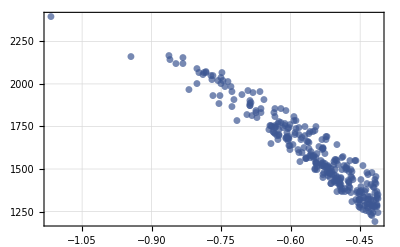

```mathematica
With[
{range = 12000},
With[
{fileName = FileNameForVotedValuesSummary[range]},
With[
{values=ReadList[fileName]},
With[
{min = Min[Map[Length[#[[1]]]&, values]],
max = Max[Map[Length[#[[1]]]&, values]]
},
Show[
Table[
ListPlot[
Sort[Table[N [{Gr[tuple[[1]]] ,Log[10,tuple[[2]]]}], {tuple, Select[values, Length[#[[1]]] == l &]}]],
AxesLabel->{"magic Graham for tuple", "Ln of nth value"},
AxesStyle->Directive[Thick, Darker[Darker[Green]],12],
AxesOrigin->{0,0},
PlotLabel->"tuple magic value vs Ln of nth voted value\nFor " <> ToString[range]<>"th voted value\n"<> ToString[Length[values]]<>" tuples",
GridLines->Automatic,
Frame->True,
PlotMarkers->Automatic,
LabelStyle->{FontFamily->"Calibri", FontSize->Larger},
ImageSize->{1000},
PlotRange->All,
PlotStyle->Directive[Opacity[0.7], ColorData["DarkRainbow"][(l-min) / (max+1-min)]]
] 
,{l, min, max}
]
]
]
]
]
]
```

```mathematica
Needs["combinatorica"]
```

```mathematica
Needs["combinatorica`"]
```

```mathematica
PrimePi[7919]
```

1000

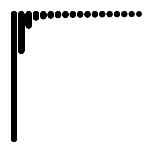

```mathematica
FerrersDiagram[Distribution[Sort[Map[IntegerPart[N [Log[10,#[[2]]]]]&,ReadList[FileNameForVotedValuesSummary[12000]]]]]]
```

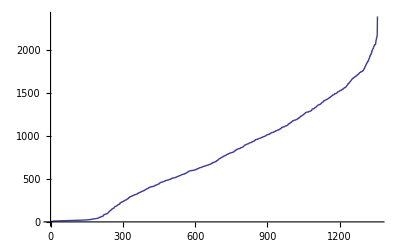

```mathematica
ListLinePlot[Sort[Map[N [Log[10,#[[2]]]]&,ReadList[FileNameForVotedValuesSummary[12000]]]]]
```

```mathematica
TableForm[Sort[Map[{N [Log[10,#[[2]]]],N[magicGraham[#[[1]]]],N[Gr[#[[1]]]],#[[1]], Fold[Times,1,#[[1]]]}&,ReadList[FileNameForVotedValuesSummary[12000]]], #1[[3]]>#2[[3]]&], TableDepth->2, TableAlignments->Right,TableHeadings->{Automatic,{"Log10 voted value", "magic","calibrated",  "tuple", "tuple product"}}]
```

| Log10 voted value | magic | calibrated | tuple | tuple product
1 | 4.59917 | 0.380493 | 0.380493 | {7283,7541,7573,7759,7823,7841,7907,7919} | 12394808614213664790331273119199
2 | 5.76307 | 0.380389 | 0.380389 | {7151,7499,7681,7691,7817,7901,7907,7919} | 12251096581096567716511641477719
3 | 4.75559 | 0.377972 | 0.377972 | {5087,7673,7873,7879,7883,7901,7907,7919} | 9442651421793001722174334711363
4 | 5.65481 | 0.374781 | 0.374781 | {4799,6733,7013,7489,7867,7879,7907,7919} | 6586419167918184245369439016711
5 | 5.01352 | 0.36982 | 0.36982 | {2551,6857,7841,7867,7883,7901,7907,7919} | 4208049910515213551585888154031
6 | 6.30758 | 0.363126 | 0.363126 | {2609,5501,5897,6971,7247,7649,7681,7829} | 1966658325602421610534587208301
7 | 6.63921 | 0.360957 | 0.360957 | {1801,5717,6577,7307,7499,7681,7753,7817} | 1727348108969031449516581998997
8 | 6.1339 | 0.356962 | 0.356962 | {1987,3343,5987,7547,7673,7867,7901,7907} | 1131842508869153913161413646513
9 | 6.48575 | 0.347222 | 0.347222 | {761,3557,7669,7723,7879,7901,7907,7919} | 624925920527055384202724834693
10 | 6.97443 | 0.342076 | 0.342076 | {911,1997,7211,7541,7591,7639,7823,7907} | 354847253932607692440130524913
11 | 11.5951 | 0.169868 | 0.169868 | {263,641,761,1009,1019,1093,1151,1171} | 194319402168388981409669
12 | 13.4818 | 0.163338 | 0.163338 | {233,683,797,877,937,991,1093,1151} | 129940122070679892624271
13 | 10.451 | 0.15326 | 0.15326 | {661,673,677,683,691,701,709,719} | 50792207348188595976103
14 | 10.3321 | 0.151868 | 0.151868 | {659,661,673,677,683,691,701,709} | 46553636498548379343883
15 | 11.0617 | 0.150601 | 0.150601 | {241,487,709,719,953,967,1009,1021} | 56801187123892406492023
16 | 10.7447 | 0.150549 | 0.150549 | {653,659,661,673,677,683,691,701} | 42876621485969099734211
17 | 13.1126 | 0.150363 | 0.150363 | {419,499,607,619,653,797,1013,1151} | 47670551943772340204759
18 | 18.1012 | 0.150034 | 0.150034 | {229,593,647,751,787,1009,1013,1033} | 54828966391067356840763
19 | 10.7424 | 0.149259 | 0.149259 | {647,653,659,661,673,677,683,691} | 39573714837977186202617
20 | 10.8447 | 0.148098 | 0.148098 | {643,647,653,659,661,673,677,683} | 36824744776873126958441
21 | 8.57943 | 0.147072 | 0.147072 | {641,643,647,653,659,661,673,677} | 34560265595864823397307
22 | 15.4226 | 0.146091 | 0.146091 | {293,443,547,599,797,1013,1031,1171} | 41454227112311315258767
23 | 9.9939 | 0.145931 | 0.145931 | {631,641,643,647,653,659,661,673} | 32212005304269872324521
24 | 12.7095 | 0.145441 | 0.145441 | {457,479,547,593,631,883,911,947} | 34131246707111026232533
25 | 10.4663 | 0.144569 | 0.144569 | {619,631,641,643,647,653,659,661} | 29627386750881205005763
26 | 14.2275 | 0.143825 | 0.143825 | {127,383,809,911,1063,1091,1187,1201} | 59268117741979695217289
27 | 15.0559 | 0.143561 | 0.143561 | {409,463,523,563,647,769,947,1217} | 31973159961207141507331
28 | 10.0383 | 0.143444 | 0.143444 | {617,619,631,641,643,647,653,659} | 27655215772002577138511
29 | 10.825 | 0.14226 | 0.14226 | {613,617,619,631,641,643,647,653} | 25724806173349893453577
30 | 10.6613 | 0.141062 | 0.141062 | {607,613,617,619,631,641,643,647} | 23912645248427848891763
31 | 10.3753 | 0.139849 | 0.139849 | {601,607,613,617,619,631,641,643} | 22212519002017213576429
32 | 17.914 | 0.139798 | 0.139798 | {199,449,521,757,787,839,1151,1217} | 32593846450771648667657
33 | 17.1765 | 0.138933 | 0.138933 | {269,487,523,607,643,719,1171,1193} | 26860174093468823562233
34 | 10.6167 | 0.138681 | 0.138681 | {599,601,607,613,617,619,631,641} | 20692533253823189630297
35 | 10.3545 | 0.137396 | 0.137396 | {593,599,601,607,613,617,619,631} | 19143014383022077146281
36 | 15.2889 | 0.136772 | 0.136772 | {113,463,797,821,907,1063,1069,1087} | 38353827787792100125769
37 | 11.1874 | 0.136199 | 0.136199 | {587,593,599,601,607,613,617,619} | 17808160765188525015637
38 | 14.1295 | 0.13525 | 0.13525 | {167,419,571,659,773,1033,1091,1181} | 27089842533410722608583
39 | 10.2354 | 0.135028 | 0.135028 | {577,587,593,599,601,607,613,617} | 16599852603414828649471
40 | 10.0726 | 0.133735 | 0.133735 | {571,577,587,593,599,601,607,613} | 15362262295866883563773
41 | 14.6964 | 0.133408 | 0.133408 | {383,439,547,571,619,727,809,857} | 16384799533740917872661
42 | 13.5042 | 0.132705 | 0.132705 | {139,619,631,661,761,857,977,1039} | 23758108314569146073861
43 | 11.1387 | 0.13249 | 0.13249 | {569,571,577,587,593,599,601,607} | 14259587677566487353649
44 | 11.1257 | 0.131228 | 0.131228 | {563,569,571,577,587,593,599,601} | 13225943760247005568541
45 | 11.1286 | 0.129949 | 0.129949 | {557,563,569,571,577,587,593,599} | 12257655032375344595137
46 | 14.9609 | 0.129237 | 0.129237 | {257,271,439,701,709,821,1163,1187} | 17222840451500021321597
47 | 14.962 | 0.129105 | 0.129105 | {257,461,503,593,739,773,823,839} | 13939347838794472758997
48 | 10.6123 | 0.128417 | 0.128417 | {547,557,563,569,571,577,587,593} | 11193551423554780456661
49 | 17.7477 | 0.1282 | 0.1282 | {293,307,509,599,691,797,907,1021} | 13986852611866055633629
50 | 13.9434 | 0.128197 | 0.128197 | {97,311,523,1061,1069,1181,1187,1201} | 30128015440116670334443
51 | 15.5765 | 0.127259 | 0.127259 | {107,587,647,709,739,821,1091,1097} | 20921430135066350631991
52 | 13.1175 | 0.126864 | 0.126864 | {541,547,557,563,569,571,577,587} | 10211992108167177448657
53 | 15.4565 | 0.126385 | 0.126385 | {271,307,439,643,677,811,859,1193} | 13213756209325635136741
54 | 12.369 | 0.124897 | 0.124897 | {523,541,547,557,563,569,571,577} | 9098589220734980929553
55 | 13.1486 | 0.123152 | 0.123152 | {521,523,541,547,557,563,569,571} | 8215537233973873594969
56 | 15.972 | 0.121799 | 0.121799 | {139,379,521,743,787,809,883,1117} | 12806123269378600686059
57 | 12.9982 | 0.121177 | 0.121177 | {509,521,523,541,547,557,563,569} | 7323482402964451243151
58 | 16.5833 | 0.120337 | 0.120337 | {181,311,419,701,761,929,947,967} | 10704042596180201260849
59 | 13.1905 | 0.119054 | 0.119054 | {503,509,521,523,541,547,557,563} | 6474009927400912083137
60 | 20.27 | 0.116977 | 0.116977 | {211,241,509,571,757,769,937,1063} | 8569361483475277452047
61 | 12.7721 | 0.11697 | 0.11697 | {499,503,509,521,523,541,547,557} | 5738065637252318169601
62 | 17.0286 | 0.115818 | 0.115818 | {109,331,509,677,863,967,1013,1061} | 11151236890013631002591
63 | 16.6143 | 0.115812 | 0.115812 | {89,359,431,751,1031,1051,1103,1129} | 13955085384237563420357
64 | 17.1089 | 0.115712 | 0.115712 | {233,349,379,491,577,839,953,1031} | 7197661030838278837877
65 | 12.9205 | 0.114783 | 0.114783 | {491,499,503,509,521,523,541,547} | 5058151217039296627063
66 | 18.4675 | 0.114646 | 0.114646 | {241,317,419,541,641,739,761,1039} | 6486198942980759957623
67 | 15.0759 | 0.11435 | 0.11435 | {179,379,449,523,661,683,967,1009} | 7017462076345661490923
68 | 17.1605 | 0.114154 | 0.114154 | {67,601,641,719,823,859,1031,1087} | 14703387501155454403097
69 | 12.9205 | 0.112761 | 0.112761 | {487,491,499,503,509,521,523,541} | 4503326586285443249323
70 | 16.0351 | 0.111567 | 0.111567 | {223,229,347,601,659,751,1117,1123} | 6611539138086847737931
71 | 15.841 | 0.110759 | 0.110759 | {223,229,571,577,691,761,773,809} | 5532774710027050537223
72 | 12.5918 | 0.110633 | 0.110633 | {479,487,491,499,503,509,521,523} | 3987233705786926647737
73 | 17.0357 | 0.110532 | 0.110532 | {113,409,487,521,613,821,1117,1153} | 7600716745341226679507
74 | 18.3882 | 0.110363 | 0.110363 | {173,347,487,547,677,739,773,883} | 5460911898157895053243
75 | 18.8347 | 0.109076 | 0.109076 | {149,257,431,601,727,887,971,1013} | 6291552716308629155941
76 | 12.865 | 0.108636 | 0.108636 | {467,479,487,491,499,503,509,521} | 3560302372088900085073
77 | 18.2266 | 0.108134 | 0.108134 | {151,223,479,503,751,947,1031,1061} | 6311742519509545930727
78 | 22.0475 | 0.107277 | 0.107277 | {109,397,479,509,643,863,967,1117} | 6323706664895795480453
79 | 18.9115 | 0.106784 | 0.106784 | {157,379,389,491,643,727,823,1109} | 4848939003086903733719
80 | 12.7468 | 0.10655 | 0.10655 | {463,467,479,487,491,499,503,509} | 3163953931434089710919
81 | 12.865 | 0.104792 | 0.104792 | {461,463,467,479,487,491,499,503} | 2865584994874489895351
82 | 17.7958 | 0.103788 | 0.103788 | {197,283,431,521,593,701,797,883} | 3662346165216815224843
83 | 17.0479 | 0.103658 | 0.103658 | {101,373,421,457,683,977,997,1187} | 5723868479317449896569
84 | 10.3011 | 0.103085 | 0.103085 | {457,461,463,467,479,487,491,499} | 2603523544050977896969
85 | 15.7847 | 0.103004 | 0.103004 | {173,233,503,593,659,673,821,887} | 3883219665370758102779
86 | 19.6573 | 0.102586 | 0.102586 | {179,199,359,569,619,823,1069,1117} | 4426232114962267005191
87 | 16.5055 | 0.101811 | 0.101811 | {89,223,541,677,787,839,1097,1213} | 6386823654812843199967
88 | 12.865 | 0.101198 | 0.101198 | {449,457,461,463,467,479,487,491} | 2342649441440659470419
89 | 17.5242 | 0.100866 | 0.100866 | {43,401,659,953,1019,1031,1039,1093} | 12919916361912682350983
90 | 17.6267 | 0.100807 | 0.100807 | {103,157,569,683,839,983,1097,1103} | 6271442804560979107639
91 | 18.9828 | 0.0996852 | 0.0996852 | {79,487,571,613,617,739,757,1051} | 4885182956153481435539
92 | 20.4162 | 0.0995663 | 0.0995663 | {149,163,487,571,701,809,937,1193} | 4281397157726323339231
93 | 14.7667 | 0.0993512 | 0.0993512 | {443,449,457,461,463,467,479,487} | 2113632795434240621987
94 | 19.9754 | 0.0985428 | 0.0985428 | {97,223,409,521,701,1153,1163,1201} | 5203645183272167513201
95 | 20.2057 | 0.098273 | 0.098273 | {103,263,463,523,569,907,1109,1153} | 4328685765332870265851
96 | 19.2599 | 0.0979402 | 0.0979402 | {199,293,367,479,503,661,701,1123} | 2682807385257148441759
97 | 15.1822 | 0.0974835 | 0.0974835 | {439,443,449,457,461,463,467,479} | 1905307591777477685939
98 | 18.6042 | 0.0974573 | 0.0974573 | {43,503,607,661,811,1093,1097,1193} | 10067338667099930925689
99 | 12.7233 | 0.0956577 | 0.0956577 | {433,439,443,449,457,461,463,467} | 1722334420124525757853
100 | 18.2724 | 0.0950008 | 0.0950008 | {137,367,389,569,613,643,677,823} | 2444040793648740978271
101 | 19.0871 | 0.0948445 | 0.0948445 | {239,311,331,389,401,523,1033,1087} | 2253781512847517226163
102 | 18.753 | 0.0947289 | 0.0947289 | {157,167,347,571,607,941,983,1103} | 3217281423506767902689
103 | 16.6259 | 0.0943915 | 0.0943915 | {107,331,347,401,797,859,863,1109} | 3229084767689087370559
104 | 12.72 | 0.0942003 | 0.0942003 | {431,433,439,443,449,457,461,463} | 1589563458401864243329
105 | 12.7233 | 0.0924642 | 0.0924642 | {421,431,433,439,443,449,457,461} | 1445369796948563383243
106 | 19.8135 | 0.0924473 | 0.0924473 | {139,349,353,401,641,673,761,997} | 2247564759776118158323
107 | 18.8889 | 0.0919027 | 0.0919027 | {47,487,563,673,743,827,1013,1103} | 5954284193299023188869
108 | 21.5911 | 0.0917366 | 0.0917366 | {89,113,727,743,797,823,1187,1213} | 5130519601223901154997
109 | 18.9679 | 0.0913167 | 0.0913167 | {61,229,617,743,797,827,971,1187} | 4864890560879682370657
110 | 12.72 | 0.0907177 | 0.0907177 | {419,421,431,433,439,443,449,457} | 1313687516098585808197
111 | 18.3372 | 0.0905795 | 0.0905795 | {109,151,523,563,733,821,991,1097} | 3170596258348705998701
112 | 15.0475 | 0.0886786 | 0.0886786 | {409,419,421,431,433,439,443,449} | 1175707208061972856789
113 | 20.4068 | 0.0882563 | 0.0882563 | {101,389,401,439,521,599,821,1223} | 2167275032333482800947
114 | 14.9986 | 0.0865889 | 0.0865889 | {401,409,419,421,431,433,439,443} | 1050019132367151705061
115 | 22.5514 | 0.0856087 | 0.0856087 | {167,251,317,367,569,593,859,1091} | 1542056879886592197199
116 | 18.4372 | 0.0848438 | 0.0848438 | {47,379,541,641,647,829,1031,1181} | 4034221472692177556729
117 | 22.6746 | 0.0846059 | 0.0846059 | {127,229,281,389,509,919,1093,1187} | 1929297933635319106267
118 | 12.5556 | 0.0845553 | 0.0845553 | {397,401,409,419,421,431,433,439} | 940987800338056945619
119 | 21.9528 | 0.0839808 | 0.0839808 | {59,433,479,503,643,719,823,1163} | 2723722257172154592587
120 | 21.2268 | 0.0828725 | 0.0828725 | {101,211,337,563,569,797,971,1049} | 1867701341384792817427
121 | 12.3105 | 0.0823019 | 0.0823019 | {389,397,401,409,419,421,431,433} | 833813791187936564569
122 | 19.5469 | 0.081981 | 0.081981 | {101,337,379,421,547,761,787,823} | 1464263143860834933061
123 | 20.293 | 0.0809917 | 0.0809917 | {31,251,883,937,953,1019,1021,1187} | 7576685411660733781939
124 | 12.3105 | 0.0800049 | 0.0800049 | {383,389,397,401,409,419,421,431} | 737530443475703704919
125 | 23.8532 | 0.0797887 | 0.0797887 | {191,199,271,311,599,709,797,1097} | 1189471744842256785551
126 | 19.5488 | 0.0795764 | 0.0795764 | {313,349,373,383,401,467,487,523} | 744336427254417229361
127 | 18.8048 | 0.0789092 | 0.0789092 | {157,179,257,431,563,863,887,937} | 1257029524104155692411
128 | 27.0158 | 0.0780878 | 0.0780878 | {107,211,223,593,643,857,907,997} | 1487715985797540058787
129 | 15.0371 | 0.0775924 | 0.0775924 | {379,383,389,397,401,409,419,421} | 648547652151488872771
130 | 22.4589 | 0.0754589 | 0.0754589 | {127,191,223,241,937,983,1009,1217} | 1474462891776420986513
131 | 15.0815 | 0.0753069 | 0.0753069 | {373,379,383,389,397,401,409,419} | 574603976846806055923
132 | 21.3973 | 0.0736976 | 0.0736976 | {67,191,523,541,599,683,967,1093} | 1565673806770139265317
133 | 25.826 | 0.0730418 | 0.0730418 | {41,353,379,503,809,857,1153,1193} | 2631266591450500763677
134 | 14.6518 | 0.0727969 | 0.0727969 | {367,373,379,383,389,397,401,409} | 503292743443383824639
135 | 16.6644 | 0.0714605 | 0.0714605 | {41,163,467,839,1019,1049,1051,1061} | 3121174676626383585139
136 | 22.5353 | 0.070778 | 0.070778 | {47,173,563,571,823,863,1093,1103} | 2238178757159572057673
137 | 16.9217 | 0.0703091 | 0.0703091 | {359,367,373,379,383,389,397,401} | 441765513193581401089
138 | 14.8148 | 0.0678626 | 0.0678626 | {353,359,367,373,379,383,389,397} | 388885850766419537617
139 | 17.1055 | 0.067628 | 0.067628 | {29,347,433,797,887,947,1039,1117} | 3385446927867648888941
140 | 22.0719 | 0.0674191 | 0.0674191 | {37,419,523,557,569,859,919,947} | 1921071599980982479999
141 | 23.0295 | 0.0662896 | 0.0662896 | {107,239,241,421,461,719,733,1093} | 689024666256267364363
142 | 24.828 | 0.0660869 | 0.0660869 | {43,199,503,643,743,919,929,991} | 1739779397421563543039
143 | 20.7939 | 0.0654168 | 0.0654168 | {67,281,457,467,577,613,733,757} | 788588328585464489053
144 | 14.8148 | 0.0653815 | 0.0653815 | {349,353,359,367,373,379,383,389} | 341866906593149669089
145 | 25.8324 | 0.064531 | 0.064531 | {89,179,383,521,593,607,619,971} | 687753482666529004267
146 | 27.3846 | 0.0635756 | 0.0635756 | {61,271,307,409,439,821,1063,1223} | 972586435609276197043
147 | 14.2231 | 0.0631726 | 0.0631726 | {347,349,353,359,367,373,379,383} | 304955826703915000447
148 | 25.578 | 0.0618305 | 0.0618305 | {131,149,241,359,557,761,809,983} | 569260364590488371459
149 | 26.6674 | 0.0613162 | 0.0613162 | {29,461,499,569,631,751,1063,1093} | 2089943079276362742881
150 | 16.7366 | 0.0606814 | 0.0606814 | {337,347,349,353,359,367,373,379} | 268329278326943486033
151 | 26.6373 | 0.0587582 | 0.0587582 | {197,257,313,359,421,443,499,523} | 276902063504108530333
152 | 18.9286 | 0.0580328 | 0.0580328 | {331,337,347,349,353,359,367,373} | 234345623024322675137
153 | 21.7275 | 0.0548211 | 0.0548211 | {317,331,337,347,349,353,359,367} | 199162365948284954473
154 | 26.914 | 0.0540928 | 0.0540928 | {53,191,229,569,619,733,1097,1171} | 768803110705335245227
155 | 33.7477 | 0.052715 | 0.052715 | {149,281,317,373,383,449,499,509} | 216234071248469861413
156 | 19.6346 | 0.0516643 | 0.0516643 | {313,317,331,337,347,349,353,359} | 169857821639817958447
157 | 24.6769 | 0.050677 | 0.050677 | {61,127,151,631,787,1103,1109,1187} | 843475305836282413241
158 | 24.6957 | 0.0506319 | 0.0506319 | {71,113,331,367,617,761,1013,1213} | 562303668993670541363
159 | 24.5064 | 0.0496331 | 0.0496331 | {167,181,197,211,307,839,941,971} | 295701084356506267727
160 | 19.5263 | 0.0488047 | 0.0488047 | {311,313,317,331,337,347,349,353} | 147147026545914721663
161 | 32.9669 | 0.0487554 | 0.0487554 | {109,131,137,379,683,701,1087,1123} | 433316865303259782511
162 | 18.4259 | 0.0460098 | 0.0460098 | {307,311,313,317,331,337,347,349} | 127972059913869177197
163 | 25.7319 | 0.04564 | 0.04564 | {127,211,251,431,443,467,521,557} | 174040648616886890149
164 | 30.1075 | 0.0437798 | 0.0437798 | {113,241,293,397,419,463,503,509} | 157338278673937356767
165 | 30.2086 | 0.0427985 | 0.0427985 | {163,193,199,389,461,491,503,521} | 144456043899095887337
166 | 26.4631 | 0.0424757 | 0.0424757 | {293,307,311,313,317,331,337,347} | 107437861188434581429
167 | 31.8355 | 0.0417465 | 0.0417465 | {67,97,373,397,647,701,761,1093} | 363055477042654478189
168 | 33.8384 | 0.0403962 | 0.0403962 | {97,107,167,479,643,659,829,929} | 270940625177649709199
169 | 34.6041 | 0.0398019 | 0.0398019 | {29,271,431,521,617,743,757,991} | 606912097081523130473
170 | 23.7867 | 0.0384484 | 0.0384484 | {131,199,347,353,389,401,433,523} | 112800782252827650929
171 | 31.9929 | 0.0384071 | 0.0384071 | {167,223,307,313,353,409,421,463} | 100708272757347315001
172 | 26.4329 | 0.0383291 | 0.0383291 | {283,293,307,311,313,317,331,337} | 87622232611893332981
173 | 32.2724 | 0.0367183 | 0.0367183 | {71,89,337,353,419,829,953,1213} | 301838904976547988701
174 | 29.0461 | 0.0355529 | 0.0355529 | {73,107,131,317,887,1031,1061,1151} | 362251496551128148199
175 | 21.5442 | 0.0346115 | 0.0346115 | {281,283,293,307,311,313,317,331} | 73061861614071295453
176 | 35.5589 | 0.0341648 | 0.0341648 | {37,83,487,587,709,787,991,1213} | 588846776287492000711
177 | 28.8998 | 0.0338891 | 0.0338891 | {211,239,293,317,331,337,373,379} | 73860658497359801801
178 | 40.5 | 0.0329719 | 0.0329719 | {127,149,193,271,373,463,829,859} | 121717803474897108041
179 | 28.895 | 0.0329532 | 0.0329532 | {131,227,281,293,349,383,499,521} | 85081191442837718053
180 | 34.9757 | 0.0327817 | 0.0327817 | {233,241,251,263,283,307,421,541} | 73351095684326010149
181 | 34.9095 | 0.0319339 | 0.0319339 | {137,227,281,293,367,409,443,457} | 77808969427022141051
182 | 35.3543 | 0.0313411 | 0.0313411 | {43,127,277,389,419,1013,1109,1217} | 337090986179043345503
183 | 19.151 | 0.0309492 | 0.0309492 | {277,281,283,293,307,311,313,317} | 61142403828089875651
184 | 36.8891 | 0.0308901 | 0.0308901 | {23,349,409,499,521,761,769,1109} | 553933183738875003757
185 | 37.9103 | 0.0297012 | 0.0297012 | {67,179,199,311,331,641,881,1151} | 159690306500600134877
186 | 35.3625 | 0.0293718 | 0.0293718 | {43,107,383,431,563,653,991,1019} | 281966615877147717163
187 | 36.3858 | 0.0291842 | 0.0291842 | {79,149,197,353,397,613,761,853} | 129312039216669188443
188 | 35.639 | 0.0289464 | 0.0289464 | {79,103,179,263,607,811,911,1103} | 189485739143401097809
189 | 45.6382 | 0.0286257 | 0.0286257 | {71,149,251,281,373,601,761,1097} | 139636593892193799109
190 | 30.8665 | 0.0284172 | 0.0284172 | {13,349,449,719,1051,1091,1181,1193} | 2366256492327389233091
191 | 26.4335 | 0.0276912 | 0.0276912 | {271,277,281,283,293,307,311,313} | 52270004534423836913
192 | 36.2593 | 0.0275088 | 0.0275088 | {13,421,607,673,739,947,1051,1213} | 1994743863604322728937
193 | 21.5145 | 0.0245331 | 0.0245331 | {269,271,277,281,283,293,307,311} | 44922144472076716069
194 | 37.8932 | 0.0218978 | 0.0218978 | {41,73,277,421,797,941,977,1217} | 311244487642175264033
195 | 27.8745 | 0.0217487 | 0.0217487 | {151,223,233,241,277,397,449,509} | 47521394140897177901
196 | 21.4436 | 0.0210217 | 0.0210217 | {263,269,271,277,281,283,293,307} | 37988823138765840277
197 | 35.4728 | 0.0203968 | 0.0203968 | {83,157,263,379,409,479,491,499} | 62346713081057852413
198 | 39.5887 | 0.0203492 | 0.0203492 | {67,71,239,263,607,821,1039,1103} | 170769264941626280351
199 | 39.3993 | 0.019804 | 0.019804 | {131,197,227,317,349,353,383,509} | 44600459170329670367
200 | 50.6493 | 0.0197152 | 0.0197152 | {47,101,317,373,463,643,857,1069} | 153086825311021191019
201 | 40.8245 | 0.019503 | 0.019503 | {41,229,239,443,479,593,607,673} | 115349290696052917601
202 | 30.5886 | 0.0172762 | 0.0172762 | {257,263,269,271,277,281,283,293} | 31801718393038504727
203 | 46.903 | 0.016864 | 0.016864 | {97,199,263,283,367,401,421,491} | 43705995784387620419
204 | 36.0463 | 0.0161497 | 0.0161497 | {59,269,281,293,421,439,461,521} | 58004741631557499277
205 | 54.0218 | 0.0155325 | 0.0155325 | {19,149,467,521,739,827,937,1213} | 478459093301586069481
206 | 42.9135 | 0.0141733 | 0.0141733 | {19,233,257,449,827,907,1031,1033} | 408094526330349713117
207 | 40.1387 | 0.013979 | 0.013979 | {251,257,263,269,271,277,281,283} | 27243110295742882889
208 | 44.3525 | 0.013495 | 0.013495 | {113,139,179,263,457,479,499,523} | 42243118470110751409
209 | 40.8389 | 0.0133144 | 0.0133144 | {37,151,349,353,419,577,601,1129} | 112911207988179761653
210 | 39.3684 | 0.0115011 | 0.0115011 | {47,283,307,347,383,443,463,499} | 55543875726387362437
211 | 43.788 | 0.0109787 | 0.0109787 | {109,163,229,293,359,409,419,439} | 32196858936708899429
212 | 39.384 | 0.0106918 | 0.0106918 | {139,193,199,269,349,367,379,401} | 27954552182279429209
213 | 40.1387 | 0.0105129 | 0.0105129 | {241,251,257,263,269,271,277,281} | 23199963184713903803
214 | 39.1542 | 0.0103813 | 0.0103813 | {31,163,167,317,691,881,883,1153} | 165794072021282734343
215 | 52.4391 | 0.0090468 | 0.0090468 | {163,197,233,277,293,331,337,349} | 23639618449129144529
216 | 64.3072 | 0.00896194 | 0.00896194 | {67,73,149,281,523,929,997,1021} | 101281133788864988741
217 | 58.7669 | 0.00805078 | 0.00805078 | {157,167,191,197,331,401,431,463} | 26130417247117779059
218 | 56.4796 | 0.00803548 | 0.00803548 | {157,173,191,223,241,401,461,509} | 26233975508249538257
219 | 51.6281 | 0.00701121 | 0.00701121 | {239,241,251,257,263,269,271,277} | 19732353028991540957
220 | 48.5467 | 0.00673927 | 0.00673927 | {97,167,191,223,353,487,491,521} | 30342357272233517747
221 | 56.6478 | 0.00630151 | 0.00630151 | {97,137,163,167,331,439,719,1151} | 43500385431836219449
222 | 53.4072 | 0.00560439 | 0.00560439 | {11,431,563,599,647,751,971,1129} | 851652767580733222291
223 | 60.9924 | 0.00476233 | 0.00476233 | {131,149,191,229,239,491,499,503} | 25146314182648774573
224 | 74.2748 | 0.00463965 | 0.00463965 | {107,137,227,263,347,379,461,479} | 25415056182317743973
225 | 66.2136 | 0.00463026 | 0.00463026 | {43,241,263,373,409,439,467,523} | 44581684710346505167
226 | 53.4877 | 0.00453777 | 0.00453777 | {107,157,241,281,283,317,439,541} | 24238976390237455331
227 | 32.7459 | 0.00324507 | 0.00324507 | {233,239,241,251,257,263,269,271} | 16597972042436927953
228 | 44.0363 | 0.00319046 | 0.00319046 | {107,157,179,241,373,409,463,467} | 23904711961126776917
229 | 64.607 | 0.00283217 | 0.00283217 | {17,139,487,541,563,859,907,1093} | 298482556410326735407
230 | 49.8822 | 0.00276047 | 0.00276047 | {19,173,283,331,727,991,1019,1049} | 237122011774095742517
231 | 49.3463 | 0.000981717 | 0.000981717 | {127,139,181,223,347,373,443,509} | 20795136445048923983
232 | 81.3369 | 0.000520543 | 0.000520543 | {113,227,233,271,277,307,331,379} | 17278851049603339523
233 | 37.4337 | 0.00027131 | 0.00027131 | {17,281,313,509,599,601,827,839} | 190101754865870698423
234 | 35.0643 | -0.000445014 | -0.000445014 | {229,233,239,241,251,257,263,269} | 14025592611505743547
235 | 59.4682 | -0.000713406 | -0.000713406 | {11,379,419,433,787,857,1051,1193} | 639635454613681190731
236 | 66.1359 | -0.000845023 | -0.000845023 | {17,229,349,461,631,659,727,997} | 188779616316175817027
237 | 55.9809 | -0.00151116 | -0.00151116 | {89,151,173,179,251,367,751,967} | 27840195769628987557
238 | 62.3419 | -0.0031552 | -0.0031552 | {137,181,227,239,277,283,359,373} | 14121875719639538317
239 | 58.2137 | -0.00352684 | -0.00352684 | {137,149,241,251,283,307,353,379} | 14352789847210649701
240 | 41.2947 | -0.00417494 | -0.00417494 | {227,229,233,239,241,251,257,263} | 11835723133129382101
241 | 65.7667 | -0.00483499 | -0.00483499 | {151,163,191,193,229,293,443,541} | 14590135390117796909
242 | 82.9764 | -0.00651103 | -0.00651103 | {71,167,181,211,313,383,409,947} | 21025786421146230979
243 | 63.023 | -0.006585 | -0.006585 | {13,149,277,821,829,863,1049,1213} | 401009039205860795671
244 | 27.5509 | -0.00782405 | -0.00782405 | {223,227,229,233,239,241,251,257} | 10035613150904381021
245 | 92.8427 | -0.00810945 | -0.00810945 | {31,41,257,769,787,827,857,1187} | 166309399898720750813
246 | 62.5637 | -0.0086212 | -0.0086212 | {107,163,227,251,269,349,353,367} | 12086190559552243367
247 | 88.2051 | -0.00922159 | -0.00922159 | {139,157,167,179,241,349,439,521} | 12549564871276796369
248 | 53.5895 | -0.0106441 | -0.0106441 | {101,109,197,229,293,421,449,509} | 14001140694323182541
249 | 68.9122 | -0.0113564 | -0.0113564 | {97,139,191,223,317,367,397,463} | 12280656644312591251
250 | 102.804 | -0.0122435 | -0.0122435 | {211,223,227,229,233,239,241,251} | 8239355544127721383
251 | 85.3505 | -0.0125201 | -0.0125201 | {31,151,241,331,347,479,593,997} | 36694292402286203723
252 | 74.3847 | -0.0128416 | -0.0128416 | {47,163,281,311,313,349,487,499} | 17772619483002659531
253 | 105.674 | -0.0133308 | -0.0133308 | {83,173,181,211,229,419,457,509} | 12239641948276820947
254 | 66.6575 | -0.0139914 | -0.0139914 | {113,191,193,251,269,271,311,379} | 8983881422852065139
255 | 98.6628 | -0.0148689 | -0.0148689 | {149,163,211,223,239,277,317,337} | 8082170802653172557
256 | 70.7451 | -0.015383 | -0.015383 | {79,151,191,293,317,353,373,379} | 10560562120714328209
257 | 97.4141 | -0.015971 | -0.015971 | {73,149,163,263,313,337,461,521} | 11813140479397568893
258 | 57.5477 | -0.0160825 | -0.0160825 | {43,89,149,241,313,709,1049,1153} | 36885624555768518507
259 | 81.8401 | -0.0175178 | -0.0175178 | {199,211,223,227,229,233,239,241} | 6532397423431938467
260 | 89.1715 | -0.0179507 | -0.0179507 | {109,139,199,257,263,281,373,379} | 8095386870871789793
261 | 68.4595 | -0.0182949 | -0.0182949 | {61,79,199,359,373,479,491,523} | 15795449068032946649
262 | 65.6978 | -0.0204305 | -0.0204305 | {131,137,151,229,257,347,353,367} | 7169810217803041877
263 | 71.5013 | -0.0206941 | -0.0206941 | {101,139,167,193,239,347,421,521} | 8231086184983587377
264 | 98.3986 | -0.0210412 | -0.0210412 | {53,137,199,251,353,431,433,487} | 11635688006170062017
265 | 85.7769 | -0.0212579 | -0.0212579 | {37,97,157,227,409,571,821,1193} | 29257821432468551957
266 | 129.221 | -0.0216778 | -0.0216778 | {37,167,179,347,419,421,461,509} | 15886035455947707877
267 | 94.2225 | -0.0220323 | -0.0220323 | {13,193,239,563,617,751,821,1031} | 132413992530477996221
268 | 100.067 | -0.0221366 | -0.0221366 | {197,199,211,223,227,229,233,239} | 5339760549444364639
269 | 107.002 | -0.0223049 | -0.0223049 | {109,149,163,229,281,293,359,373} | 6683640372994817017
270 | 94.7971 | -0.0225352 | -0.0225352 | {37,71,193,349,373,613,769,911} | 28343718876602595649
271 | 137.27 | -0.0229775 | -0.0229775 | {79,107,193,241,313,347,373,541} | 8617179305705476447
272 | 79.7189 | -0.0245695 | -0.0245695 | {47,179,181,283,353,383,409,419} | 9984508927591026071
273 | 85.9429 | -0.0249691 | -0.0249691 | {107,151,167,197,283,311,347,367} | 5957798158721370791
274 | 109.41 | -0.0255325 | -0.0255325 | {79,181,197,227,251,313,337,367} | 6213149070649776737
275 | 150.477 | -0.0259511 | -0.0259511 | {113,149,157,179,229,271,449,461} | 6078122306589574061
276 | 99.0098 | -0.0264237 | -0.0264237 | {131,173,181,199,223,241,317,359} | 4992575790743875513
277 | 114.239 | -0.0269034 | -0.0269034 | {103,127,163,251,257,311,359,373} | 5727947968700501917
278 | 88.6371 | -0.0270583 | -0.0270583 | {193,197,199,211,223,227,229,233} | 4312024209383942993
279 | 112.06 | -0.0271359 | -0.0271359 | {47,139,211,251,359,367,419,491} | 9378316017177333581
280 | 93.1087 | -0.0273158 | -0.0273158 | {103,157,181,229,263,269,293,373} | 5182453511203152857
281 | 123.832 | -0.0286386 | -0.0286386 | {61,199,211,251,277,283,331,367} | 6122084939371081553
282 | 127.52 | -0.0287118 | -0.0287118 | {79,181,193,211,233,293,367,373} | 5441816183996209183
283 | 125.608 | -0.0292167 | -0.0292167 | {137,181,197,211,223,241,271,277} | 4158328445063693119
284 | 113.768 | -0.0292508 | -0.0292508 | {89,103,173,229,307,311,373,467} | 6039949308023213173
285 | 91.4003 | -0.0297896 | -0.0297896 | {101,163,199,233,263,269,271,307} | 4492971569301945439
286 | 90.1125 | -0.0305831 | -0.0305831 | {79,163,193,241,283,293,311,317} | 4896240640804634153
287 | 134.253 | -0.0310575 | -0.0310575 | {41,139,181,311,349,373,419,521} | 9116405320277395507
288 | 171.48 | -0.0314207 | -0.0314207 | {137,173,193,211,223,229,263,293} | 3798132828383292319
289 | 137.992 | -0.0314992 | -0.0314992 | {53,151,193,197,269,383,457,487} | 6977061760114149859
290 | 123.042 | -0.0315772 | -0.0315772 | {109,149,167,181,229,277,293,499} | 4552932689500478117
291 | 86.0741 | -0.0316619 | -0.0316619 | {191,193,197,199,211,223,227,229} | 3534749459194562711
292 | 143.062 | -0.0318191 | -0.0318191 | {97,113,191,233,241,311,347,373} | 4732114061879600423
293 | 120.89 | -0.0320543 | -0.0320543 | {47,163,227,277,311,337,359,367} | 6651841484971532749
294 | 110.382 | -0.0324281 | -0.0324281 | {13,139,269,503,599,619,853,1051} | 81273251743137510407
295 | 125.561 | -0.0326629 | -0.0326629 | {97,101,179,197,251,337,383,449} | 5025289692024735319
296 | 142.412 | -0.0327751 | -0.0327751 | {97,107,197,211,263,313,349,373} | 4623155894092982459
297 | 152.728 | -0.0336147 | -0.0336147 | {149,157,173,193,233,251,269,283} | 3477424351046882057
298 | 135.982 | -0.0336821 | -0.0336821 | {103,113,179,199,277,317,337,349} | 4281699011954916023
299 | 161.692 | -0.0341087 | -0.0341087 | {61,167,197,263,271,293,317,367} | 4875627506467676369
300 | 187.266 | -0.0343451 | -0.0343451 | {37,89,97,103,857,887,1129,1153} | 32555800662756614429
301 | 135.673 | -0.03459 | -0.03459 | {127,137,139,163,263,311,347,349} | 3904790445929919097
302 | 198.501 | -0.0352346 | -0.0352346 | {41,109,239,263,311,347,503,523} | 7974868706819526709
303 | 112.57 | -0.035428 | -0.035428 | {107,139,149,191,239,241,331,491} | 3962257015388614853
304 | 187.606 | -0.0357589 | -0.0357589 | {53,101,173,211,281,463,521,523} | 6927117030382963691
305 | 150.948 | -0.0359831 | -0.0359831 | {37,101,131,197,389,479,751,997} | 13454911010381018063
306 | 167.545 | -0.0365255 | -0.0365255 | {97,179,193,197,211,257,281,337} | 3390003134935220437
307 | 161.537 | -0.037176 | -0.037176 | {181,191,193,197,199,211,223,227} | 2793841275607929479
308 | 123.695 | -0.0374461 | -0.0374461 | {7,443,449,467,607,773,1039,1063} | 336962820623520580741
309 | 208.33 | -0.0378713 | -0.0378713 | {83,149,167,227,241,271,331,353} | 3577632455739163319
310 | 138.298 | -0.0381568 | -0.0381568 | {101,127,191,197,241,263,313,347} | 3322548212289478877
311 | 183.892 | -0.0382257 | -0.0382257 | {89,97,173,179,241,347,421,449} | 4226061659266882313
312 | 137.782 | -0.0384033 | -0.0384033 | {89,103,197,223,251,293,331,379} | 3715411030668304939
313 | 141.047 | -0.038516 | -0.038516 | {107,139,167,191,193,223,397,419} | 3396370954092454537
314 | 155.071 | -0.0388576 | -0.0388576 | {79,113,199,227,283,307,317,331} | 3676178031093289877
315 | 154.372 | -0.0389973 | -0.0389973 | {53,197,199,233,251,313,317,349} | 4207787909536684013
316 | 130.636 | -0.0395125 | -0.0395125 | {83,181,191,223,229,271,277,281} | 3090905730516540737
317 | 133.375 | -0.0398507 | -0.0398507 | {31,193,271,307,311,337,349,379} | 6900516457950878747
318 | 154.057 | -0.0401731 | -0.0401731 | {61,89,223,227,313,317,331,523} | 4720454809090826957
319 | 159.302 | -0.0415335 | -0.0415335 | {13,181,191,337,569,641,827,1061} | 48470375549967806513
320 | 195.403 | -0.041605 | -0.041605 | {29,137,181,307,421,433,449,467} | 8438567509758768229
321 | 200.467 | -0.0416806 | -0.0416806 | {71,151,197,223,263,281,293,307} | 3130937868842789003
322 | 147.482 | -0.0427637 | -0.0427637 | {179,181,191,193,197,199,211,223} | 2203073076360437783
323 | 179.456 | -0.0436971 | -0.0436971 | {61,89,127,241,263,443,467,521} | 4710366327800865989
324 | 195.332 | -0.044068 | -0.044068 | {89,107,151,193,263,331,349,353} | 2976404244857247949
325 | 177.139 | -0.0441264 | -0.0441264 | {61,167,223,229,241,257,293,317} | 2992703558394435913
326 | 183.87 | -0.0441604 | -0.0441604 | {41,223,233,239,251,269,311,379} | 4051987922536285651
327 | 150.697 | -0.0441671 | -0.0441671 | {61,101,127,239,281,409,431,449} | 4159164233724914783
328 | 192.295 | -0.0443489 | -0.0443489 | {79,107,179,229,251,263,349,373} | 2977577753483775823
329 | 157.956 | -0.0445198 | -0.0445198 | {67,103,199,269,281,283,293,373} | 3210602883533621357
330 | 127.368 | -0.0450161 | -0.0450161 | {67,83,101,227,307,461,509,521} | 4785143129147660341
331 | 150.661 | -0.0451311 | -0.0451311 | {67,101,181,263,281,307,313,367} | 3192166951427708057
332 | 154.38 | -0.045337 | -0.045337 | {59,109,181,211,277,347,367,401} | 3474235234797942233
333 | 178.09 | -0.0456726 | -0.0456726 | {83,103,107,191,241,379,421,521} | 3500326320755162887
334 | 188.902 | -0.0457213 | -0.0457213 | {71,113,163,241,251,317,337,347} | 2932471490142046217
335 | 158.783 | -0.0457756 | -0.0457756 | {41,163,179,269,307,337,347,349} | 4031809002154632841
336 | 178.385 | -0.0459811 | -0.0459811 | {79,103,127,263,277,307,349,373} | 3008681313867272111
337 | 174.084 | -0.0461888 | -0.0461888 | {61,139,163,191,229,311,337,503} | 3186833429471747663
338 | 198.686 | -0.046364 | -0.046364 | {109,127,157,163,181,311,347,349} | 2414967782761999249
339 | 143.79 | -0.047927 | -0.047927 | {61,71,223,263,281,307,379,433} | 3596007567272760011
340 | 200.825 | -0.0480356 | -0.0480356 | {47,101,131,163,443,463,467,491} | 4767176391980981743
341 | 198.788 | -0.048452 | -0.048452 | {61,71,83,353,359,461,491,503} | 5186636746681817663
342 | 185.262 | -0.0487881 | -0.0487881 | {173,179,181,191,193,197,199,211} | 1709110503185451733
343 | 222.374 | -0.0488316 | -0.0488316 | {73,151,167,181,239,269,293,373} | 2341108202206108879
344 | 235.941 | -0.0496726 | -0.0496726 | {47,109,167,211,307,353,379,479} | 3551494010390745361
345 | 180.983 | -0.0497617 | -0.0497617 | {79,127,149,227,229,269,317,337} | 2233160118511177411
346 | 206.003 | -0.0503614 | -0.0503614 | {67,79,223,257,269,313,317,337} | 2728510698600412499
347 | 184.179 | -0.0508907 | -0.0508907 | {37,73,211,293,317,383,491,523} | 5206140411555122929
348 | 202.793 | -0.051087 | -0.051087 | {71,89,179,199,239,241,421,491} | 2679988893626463011
349 | 191.088 | -0.0511036 | -0.0511036 | {79,89,109,193,233,373,461,499} | 2957107608748400297
350 | 174.765 | -0.0526152 | -0.0526152 | {29,181,197,293,313,347,349,367} | 4214787882953416177
351 | 196.029 | -0.0530287 | -0.0530287 | {67,73,137,251,293,359,383,421} | 2852560671097325297
352 | 176.175 | -0.0532925 | -0.0532925 | {79,103,113,211,223,311,401,431} | 2325477327322466413
353 | 192.477 | -0.0534744 | -0.0534744 | {89,103,109,149,269,307,397,479} | 2338065498773613163
354 | 206.091 | -0.0537842 | -0.0537842 | {61,107,191,229,241,281,311,367} | 2206644022235782981
355 | 198.839 | -0.0538708 | -0.0538708 | {43,113,139,191,281,397,479,499} | 3439758498077923927
356 | 179.68 | -0.053957 | -0.053957 | {61,173,191,211,223,263,271,283} | 1912969732760465921
357 | 227.638 | -0.0544232 | -0.0544232 | {167,173,179,181,191,193,197,199} | 1352708312947727201
358 | 180.924 | -0.0551567 | -0.0551567 | {97,139,163,181,211,223,233,359} | 1565634568366642159
359 | 253.003 | -0.0553995 | -0.0553995 | {47,109,197,223,281,311,347,367} | 2504711403606885467
360 | 185.876 | -0.0560252 | -0.0560252 | {101,131,149,197,223,241,263,269} | 1476641596290468403
361 | 204.167 | -0.056639 | -0.056639 | {37,151,167,281,293,313,317,359} | 2736321552189326723
362 | 217.886 | -0.0569351 | -0.0569351 | {97,103,181,191,233,251,269,277} | 1505159737796435719
363 | 194.628 | -0.0580271 | -0.0580271 | {23,139,191,337,347,373,383,499} | 5090301782455350673
364 | 222.213 | -0.0581871 | -0.0581871 | {43,97,113,233,347,389,449,461} | 3068321737722978433
365 | 241.39 | -0.0582938 | -0.0582938 | {71,101,127,173,293,331,347,353} | 1871670265320092773
366 | 235.182 | -0.0584404 | -0.0584404 | {61,83,137,197,251,269,491,521} | 2360151804535898063
367 | 224.147 | -0.0592995 | -0.0592995 | {163,167,173,179,181,191,193,197} | 1107997261359193637
368 | 206.089 | -0.0598903 | -0.0598903 | {103,113,149,181,193,233,283,331} | 1322233544420001167
369 | 200.968 | -0.0598944 | -0.0598944 | {83,97,107,211,269,271,337,373} | 1665621672835396973
370 | 251.223 | -0.0600249 | -0.0600249 | {41,67,73,79,701,977,1033,1123} | 12586392483520491107
371 | 250.477 | -0.0601684 | -0.0601684 | {97,127,157,167,211,227,281,293} | 1273719599246377561
372 | 239.458 | -0.0609943 | -0.0609943 | {29,163,199,211,241,293,439,503} | 3094840718831374463
373 | 228.999 | -0.0610595 | -0.0610595 | {61,83,173,233,241,269,359,379} | 1800167566022027723
374 | 268.424 | -0.0613192 | -0.0613192 | {43,149,199,223,233,239,317,373} | 1872123864778743913
375 | 213.627 | -0.0613618 | -0.0613618 | {37,73,157,307,311,389,409,499} | 3214374366383284411
376 | 232.751 | -0.0621559 | -0.0621559 | {43,127,151,211,281,317,347,367} | 1973752532668406033
377 | 238.003 | -0.0622697 | -0.0622697 | {13,281,307,353,373,401,409,433} | 10486417920185178803
378 | 237.403 | -0.0623212 | -0.0623212 | {41,53,227,239,379,397,401,463} | 3293355134769183161
379 | 203.767 | -0.0626075 | -0.0626075 | {29,113,173,257,313,347,409,491} | 3177856486059711073
380 | 195.745 | -0.0628886 | -0.0628886 | {107,131,137,149,157,269,311,313} | 1176301275379376299
381 | 218.102 | -0.0632781 | -0.0632781 | {101,107,137,149,181,233,359,379} | 1265843866080719923
382 | 237.564 | -0.0633055 | -0.0633055 | {71,73,191,197,227,277,349,367} | 1570644579048779137
383 | 223.058 | -0.0637055 | -0.0637055 | {97,113,127,151,191,263,313,373} | 1232744663292177149
384 | 256.38 | -0.0637827 | -0.0637827 | {7,67,587,683,827,937,1123,1193} | 195207701586748572589
385 | 238.855 | -0.0643429 | -0.0643429 | {61,73,223,229,251,269,281,367} | 1583402864072314463
386 | 265.836 | -0.0645835 | -0.0645835 | {29,191,223,229,233,271,359,367} | 2353192390080543727
387 | 237.091 | -0.0646749 | -0.0646749 | {47,163,167,179,199,269,337,373} | 1540987278891073063
388 | 217.949 | -0.0648285 | -0.0648285 | {67,71,113,127,353,401,433,499} | 2087963179872577057
389 | 237.861 | -0.0648912 | -0.0648912 | {157,163,167,173,179,181,191,193} | 883023198139052797
390 | 254.902 | -0.0649136 | -0.0649136 | {71,103,107,191,211,263,367,491} | 1494508806587981501
391 | 254.931 | -0.0652452 | -0.0652452 | {79,89,127,131,277,337,353,373} | 1437756440374096307
392 | 264.645 | -0.0653221 | -0.0653221 | {59,79,139,167,277,317,409,449} | 1744693144691682217
393 | 247.177 | -0.0654613 | -0.0654613 | {19,131,137,193,251,577,757,1097} | 7915070991752981167
394 | 245.217 | -0.0659513 | -0.0659513 | {23,107,149,277,401,421,491,499} | 4201323829672231817
395 | 263.972 | -0.0665886 | -0.0665886 | {41,101,211,241,257,269,313,373} | 1699586610675280447
396 | 293.909 | -0.0671213 | -0.0671213 | {47,89,223,229,233,281,317,347} | 1538435128218792547
397 | 268.227 | -0.0672261 | -0.0672261 | {41,89,193,269,277,307,311,349} | 1748587674934731793
398 | 241.362 | -0.0675484 | -0.0675484 | {83,109,127,211,227,241,277,281} | 1032332869028888381
399 | 257.574 | -0.0683077 | -0.0683077 | {19,59,311,409,431,439,491,523} | 6928102127645022223
400 | 246.259 | -0.0684386 | -0.0684386 | {43,79,127,277,331,337,373,379} | 1884451538150826187
401 | 308.536 | -0.0688172 | -0.0688172 | {73,79,127,181,241,313,349,359} | 1252891615494902087
402 | 274.697 | -0.0690782 | -0.0690782 | {109,113,139,151,167,229,293,311} | 900900134672233057
403 | 231.146 | -0.0691203 | -0.0691203 | {79,103,109,173,223,269,317,379} | 1105840604207318669
404 | 232.932 | -0.0695231 | -0.0695231 | {13,89,157,271,439,839,967,991} | 17375163975662469223
405 | 293.718 | -0.0708086 | -0.0708086 | {101,131,151,157,167,197,233,337} | 810284979527967143
406 | 245.229 | -0.071 | -0.071 | {151,157,163,167,173,179,181,191} | 690862709424854779
407 | 273.553 | -0.0710224 | -0.0710224 | {53,151,179,193,197,223,269,311} | 1016124481892673089
408 | 269.588 | -0.0728052 | -0.0728052 | {47,113,127,181,257,307,311,409} | 1225219197787106257
409 | 303.13 | -0.0728713 | -0.0728713 | {89,101,103,107,283,313,331,349} | 1013716642788285269
410 | 255.728 | -0.0730625 | -0.0730625 | {89,103,107,149,197,233,367,373} | 918320587452512471
411 | 290.195 | -0.0733033 | -0.0733033 | {61,73,109,163,277,281,449,491} | 1357627791150327533
412 | 348.401 | -0.073616 | -0.073616 | {5,337,419,541,619,743,971,977} | 166649666807817879485
413 | 232.797 | -0.0736168 | -0.0736168 | {97,113,163,193,197,199,223,233} | 702384918358413023
414 | 300.924 | -0.0737898 | -0.0737898 | {71,83,97,223,263,269,317,367} | 1049171279182560539
415 | 309.314 | -0.0740203 | -0.0740203 | {97,101,107,113,157,263,443,461} | 998884747550702611
416 | 254.188 | -0.0743332 | -0.0743332 | {43,101,151,179,263,317,337,373} | 1230193848470119237
417 | 266.319 | -0.0765295 | -0.0765295 | {23,149,167,191,281,337,401,521} | 2162630180725053803
418 | 316.531 | -0.0766421 | -0.0766421 | {47,67,149,167,263,277,449,541} | 1386610625553741953
419 | 283.894 | -0.0772067 | -0.0772067 | {149,151,157,163,167,173,179,181} | 538945254996352681
420 | 290.662 | -0.0773682 | -0.0773682 | {61,137,167,179,191,211,251,283} | 715147926600842333
421 | 317.291 | -0.0778387 | -0.0778387 | {53,113,139,173,199,271,293,379} | 862470827103990229
422 | 301.081 | -0.0781312 | -0.0781312 | {43,151,167,173,181,239,307,367} | 914300364057014273
423 | 284.216 | -0.0786464 | -0.0786464 | {71,79,149,193,227,239,271,317} | 751763660736620123
424 | 259.148 | -0.0788216 | -0.0788216 | {43,73,181,199,229,281,331,479} | 1153528360280877241
425 | 303.582 | -0.0796355 | -0.0796355 | {41,127,179,193,197,229,293,379} | 901169441575444219
426 | 264.298 | -0.0799442 | -0.0799442 | {53,103,137,157,179,311,347,373} | 846028591943090909
427 | 258.472 | -0.0799707 | -0.0799707 | {29,139,179,239,241,257,313,367} | 1226942747366591797
428 | 307.789 | -0.0802127 | -0.0802127 | {59,137,167,179,193,223,227,271} | 639733953202864397
429 | 293.567 | -0.0804966 | -0.0804966 | {41,97,131,167,271,311,373,379} | 1036623570421221283
430 | 279.55 | -0.0805471 | -0.0805471 | {19,149,151,281,311,347,367,503} | 2393023974921638837
431 | 266.262 | -0.0814496 | -0.0814496 | {41,97,139,167,263,311,349,367} | 967151458570016719
432 | 315.872 | -0.08161 | -0.08161 | {31,127,179,227,263,271,293,317} | 1059000645678445073
433 | 300.723 | -0.0817729 | -0.0817729 | {53,83,103,191,257,313,353,359} | 882208359678948889
434 | 315.992 | -0.0821453 | -0.0821453 | {43,83,139,263,269,277,281,331} | 904239468764076919
435 | 319.543 | -0.0824724 | -0.0824724 | {71,83,149,181,199,229,281,307} | 624790674187781869
436 | 315.992 | -0.0826687 | -0.0826687 | {67,73,139,163,263,269,281,317} | 698350869310095853
437 | 322.199 | -0.0828238 | -0.0828238 | {71,101,127,137,211,241,281,347} | 618641860380192653
438 | 296.808 | -0.0830971 | -0.0830971 | {71,103,109,173,229,239,251,317} | 600529769962112957
439 | 329.773 | -0.0831257 | -0.0831257 | {29,67,239,269,277,313,347,379} | 1424346894163578169
440 | 289.866 | -0.0832705 | -0.0832705 | {59,67,127,233,251,269,311,313} | 768806744102490791
441 | 324.667 | -0.0834124 | -0.0834124 | {43,79,173,233,239,263,281,349} | 844078750868025509
442 | 334.556 | -0.0834488 | -0.0834488 | {37,61,227,239,251,307,337,353} | 1122462964518206317
443 | 312.568 | -0.0837918 | -0.0837918 | {107,113,131,151,163,167,241,307} | 481692581368853017
444 | 296.08 | -0.0838396 | -0.0838396 | {79,83,127,163,193,263,271,313} | 584417476886062249
445 | 339.92 | -0.083948 | -0.083948 | {139,149,151,157,163,167,173,179} | 413886135052447639
446 | 318.646 | -0.0839705 | -0.0839705 | {23,131,191,223,281,311,353,359} | 1421258990281997213
447 | 325.674 | -0.0852968 | -0.0852968 | {37,107,163,199,233,251,317,337} | 802315141063599781
448 | 329.455 | -0.0857948 | -0.0857948 | {59,61,139,199,239,281,307,353} | 724547771517560671
449 | 308.71 | -0.0861031 | -0.0861031 | {13,71,163,229,281,739,1123,1153} | 9263702717728061941
450 | 336.561 | -0.0861129 | -0.0861129 | {43,71,173,199,227,271,337,373} | 812755401733036127
451 | 361.034 | -0.0866574 | -0.0866574 | {7,157,223,479,503,523,739,1201} | 27409126080618200653
452 | 338.882 | -0.0868369 | -0.0868369 | {41,61,113,239,271,277,433,479} | 1051628883889919383
453 | 305.499 | -0.0869558 | -0.0869558 | {53,103,113,131,227,307,311,373} | 653275373555982659
454 | 308.874 | -0.0873901 | -0.0873901 | {17,61,103,163,367,839,1129,1193} | 7220478783010530473
455 | 289.455 | -0.0876356 | -0.0876356 | {31,163,173,193,197,223,241,457} | 816313619188971499
456 | 320.019 | -0.0876827 | -0.0876827 | {13,73,181,251,353,509,727,1223} | 6887662597474822423
457 | 315.306 | -0.0881528 | -0.0881528 | {37,89,137,227,263,283,307,331} | 774545095571198851
458 | 275.272 | -0.0884436 | -0.0884436 | {71,73,151,157,211,223,251,359} | 520970697827755037
459 | 369.399 | -0.0884741 | -0.0884741 | {5,263,379,421,571,673,947,971} | 74142536561062362535
460 | 302.213 | -0.0886917 | -0.0886917 | {31,67,191,229,257,283,389,409} | 1051230164654267393
461 | 345.806 | -0.0889123 | -0.0889123 | {59,97,163,181,191,227,233,281} | 479304372114449009
462 | 358.89 | -0.0895663 | -0.0895663 | {29,67,101,283,313,389,419,479} | 1357138231885176233
463 | 334.512 | -0.0896247 | -0.0896247 | {73,97,107,173,197,233,239,317} | 455830924800796033
464 | 345.249 | -0.090261 | -0.090261 | {53,97,137,163,193,197,331,367} | 530241076714929407
465 | 280.439 | -0.0906014 | -0.0906014 | {43,59,97,211,293,317,379,503} | 919408965455526463
466 | 354.324 | -0.0908062 | -0.0908062 | {137,139,149,151,157,163,167,173} | 316773187163046517
467 | 324.163 | -0.0909777 | -0.0909777 | {43,137,149,151,193,211,293,337} | 532953751974076487
468 | 367.573 | -0.0910256 | -0.0910256 | {37,89,113,151,163,421,431,541} | 899065550242335647
469 | 365.216 | -0.0914929 | -0.0914929 | {11,29,193,631,751,773,1117,1187} | 29902030098674931109
470 | 309.341 | -0.0916616 | -0.0916616 | {43,47,79,233,337,373,503,521} | 1225444838308496161
471 | 382.119 | -0.0925181 | -0.0925181 | {31,53,211,251,281,313,347,379} | 1006498385130192547
472 | 327.201 | -0.0931622 | -0.0931622 | {59,79,83,211,251,263,281,347} | 525417961669999963
473 | 318.913 | -0.0938992 | -0.0938992 | {7,83,149,571,773,907,991,1009} | 34653739848479668091
474 | 285.936 | -0.0944032 | -0.0944032 | {37,89,137,229,233,251,263,367} | 583175453094051827
475 | 385.15 | -0.0944309 | -0.0944309 | {29,71,137,211,233,307,439,509} | 951340461540134753
476 | 351.091 | -0.095477 | -0.095477 | {31,97,107,199,227,251,421,499} | 766394716958354333
477 | 357.983 | -0.0961864 | -0.0961864 | {47,61,137,193,229,269,331,349} | 539444478457527893
478 | 352.827 | -0.097042 | -0.097042 | {29,61,211,227,233,293,367,379} | 804572086022226481
479 | 342.541 | -0.0971387 | -0.0971387 | {29,79,211,239,251,257,283,313} | 660150662286294967
480 | 297.018 | -0.0972558 | -0.0972558 | {47,83,101,137,277,313,317,337} | 499955281899976673
481 | 341.006 | -0.0972636 | -0.0972636 | {53,113,131,157,179,199,241,347} | 366925492563656021
482 | 339.808 | -0.0974456 | -0.0974456 | {41,53,127,179,317,347,349,353} | 669430272175957627
483 | 377.692 | -0.0975343 | -0.0975343 | {29,73,137,197,229,347,379,461} | 793254864150269561
484 | 392.312 | -0.0980374 | -0.0980374 | {131,137,139,149,151,157,163,167} | 239868713978954299
485 | 348.282 | -0.0981573 | -0.0981573 | {67,79,127,157,163,241,271,311} | 349413430638787421
486 | 361.51 | -0.0982687 | -0.0982687 | {73,83,89,139,163,293,307,347} | 381354463973761279
487 | 345.796 | -0.098314 | -0.098314 | {59,73,97,107,211,307,367,467} | 496288439968640309
488 | 385.327 | -0.0985705 | -0.0985705 | {59,73,83,157,211,241,401,409} | 468079687380913703
489 | 362.157 | -0.0989797 | -0.0989797 | {59,83,107,127,179,263,337,379} | 400124821094313443
490 | 369.139 | -0.0990966 | -0.0990966 | {23,101,103,179,311,331,449,499} | 987812994469671641
491 | 360.153 | -0.099153 | -0.099153 | {13,107,241,257,317,379,439,479} | 2176585851237179161
492 | 386.373 | -0.0994927 | -0.0994927 | {31,101,137,197,211,283,317,337} | 539048590572417043
493 | 331.024 | -0.099885 | -0.099885 | {37,67,109,193,197,331,379,479} | 617346907610952601
494 | 379.383 | -0.100052 | -0.100052 | {29,83,139,227,241,283,313,379} | 614474370498314951
495 | 378.315 | -0.100584 | -0.100584 | {41,67,127,151,211,331,367,379} | 511746700198959647
496 | 321.323 | -0.100843 | -0.100843 | {79,101,103,157,181,191,229,263} | 268651033188291353
497 | 413.017 | -0.101219 | -0.101219 | {53,79,101,151,163,307,347,359} | 398062425746285941
498 | 396.996 | -0.101235 | -0.101235 | {23,47,251,263,337,349,359,367} | 1105785789711916217
499 | 368.776 | -0.101643 | -0.101643 | {17,137,193,241,251,257,317,461} | 1021200156144351643
500 | 345.627 | -0.101738 | -0.101738 | {37,73,109,113,311,317,421,431} | 595125477380528929
501 | 386.535 | -0.101753 | -0.101753 | {5,227,277,439,547,593,797,1033} | 36858767878265060755
502 | 386.282 | -0.102022 | -0.102022 | {31,97,101,109,281,383,401,461} | 658615112424522389
503 | 345.538 | -0.102649 | -0.102649 | {61,109,139,149,151,179,199,373} | 276279898707795937
504 | 355.716 | -0.10272 | -0.10272 | {53,113,127,131,151,241,271,307} | 301669209954898811
505 | 407.512 | -0.104175 | -0.104175 | {23,127,149,233,239,269,283,307} | 566433249433262447
506 | 417.935 | -0.104773 | -0.104773 | {29,97,113,233,251,257,281,359} | 481960792656727481
507 | 369.967 | -0.10524 | -0.10524 | {127,131,137,139,149,151,157,163} | 182415129792378419
508 | 364.866 | -0.105371 | -0.105371 | {47,101,127,157,193,229,239,283} | 282943507473477737
509 | 341.22 | -0.105491 | -0.105491 | {13,89,139,223,331,367,569,947} | 2347520133503250719
510 | 382.439 | -0.10634 | -0.10634 | {19,103,131,277,307,311,313,367} | 778845036764920753
511 | 390.443 | -0.106888 | -0.106888 | {59,73,101,137,167,227,359,373} | 302525802345449017
512 | 360.323 | -0.107419 | -0.107419 | {43,73,131,181,197,239,241,379} | 320082231314855573
513 | 411.02 | -0.107444 | -0.107444 | {37,79,83,199,257,283,337,347} | 410618884328379119
514 | 388.585 | -0.107854 | -0.107854 | {53,131,139,149,151,163,233,271} | 223479657717149707
515 | 407.964 | -0.107902 | -0.107902 | {83,109,131,139,151,163,191,241} | 186640396217113469
516 | 378.056 | -0.107998 | -0.107998 | {31,43,131,199,283,317,443,499} | 689135291194625879
517 | 359.72 | -0.108889 | -0.108889 | {37,53,181,197,211,239,317,353} | 394581499186201433
518 | 348.858 | -0.109043 | -0.109043 | {31,59,151,197,257,263,349,353} | 453049737491005301
519 | 405.514 | -0.109516 | -0.109516 | {37,101,107,127,223,239,347,349} | 327769291405834963
520 | 384.19 | -0.110109 | -0.110109 | {31,41,181,197,277,311,373,397} | 578135780231733629
521 | 371.888 | -0.110669 | -0.110669 | {31,73,107,191,239,313,337,349} | 406910845352036321
522 | 415.222 | -0.110861 | -0.110861 | {59,67,79,181,211,239,277,337} | 266086295160477787
523 | 392.525 | -0.111012 | -0.111012 | {29,61,89,181,269,373,409,487} | 569521069458470891
524 | 412.467 | -0.111355 | -0.111355 | {31,107,149,151,157,269,293,349} | 322295073406587223
525 | 397.828 | -0.111591 | -0.111591 | {41,59,139,173,193,241,311,373} | 313863160879835527
526 | 363.996 | -0.112405 | -0.112405 | {71,101,107,127,163,181,197,317} | 179539035917978993
527 | 376.341 | -0.112412 | -0.112412 | {19,109,167,173,271,313,317,347} | 558270961521632197
528 | 419.387 | -0.112416 | -0.112416 | {13,131,163,263,269,307,367,499} | 1104117430880687873
529 | 417.79 | -0.112614 | -0.112614 | {19,127,163,179,239,241,347,379} | 533312282150693987
530 | 442.028 | -0.112842 | -0.112842 | {19,89,131,199,227,373,409,431} | 657965688734480911
531 | 423.547 | -0.113266 | -0.113266 | {29,53,139,191,251,337,347,379} | 453935702843331503
532 | 384.757 | -0.113546 | -0.113546 | {59,71,103,137,193,199,271,353} | 217181352763645339
533 | 398.189 | -0.113857 | -0.113857 | {43,79,149,167,193,211,227,283} | 221131363325580893
534 | 356.27 | -0.113993 | -0.113993 | {59,89,107,139,167,181,257,313} | 189894813449769161
535 | 374.826 | -0.114038 | -0.114038 | {59,71,97,113,179,251,331,337} | 230115135765402527
536 | 417.745 | -0.114562 | -0.114562 | {41,109,113,157,181,191,239,331} | 216833453766935431
537 | 413.117 | -0.114749 | -0.114749 | {29,53,73,257,271,347,431,491} | 573835456110807889
538 | 411.111 | -0.115123 | -0.115123 | {113,127,131,137,139,149,151,157} | 126459568506372769
539 | 389.418 | -0.115414 | -0.115414 | {41,43,193,197,229,239,271,307} | 305222747303682161
540 | 403.93 | -0.116324 | -0.116324 | {59,79,89,127,193,239,277,283} | 190499677627219931
541 | 454.879 | -0.1165 | -0.1165 | {41,47,131,163,229,233,359,389} | 306602765636621017
542 | 427.071 | -0.116962 | -0.116962 | {71,73,89,103,113,313,353,359} | 212961145997930543
543 | 412.54 | -0.117501 | -0.117501 | {17,47,181,199,229,419,461,863} | 1098600157642345433
544 | 420.092 | -0.117565 | -0.117565 | {31,113,127,139,181,239,293,311} | 243760394304610363
545 | 396.961 | -0.117642 | -0.117642 | {61,97,137,151,157,181,193,211} | 141650161924119689
546 | 427.477 | -0.117651 | -0.117651 | {11,197,229,251,257,271,331,367} | 1053815512833222667
547 | 411.714 | -0.118017 | -0.118017 | {47,71,103,137,179,251,281,353} | 209856186334550879
548 | 403.367 | -0.118143 | -0.118143 | {31,103,137,173,191,233,257,263} | 227637469358486989
549 | 447.861 | -0.118555 | -0.118555 | {41,97,107,131,191,229,257,311} | 194882582589060277
550 | 416.232 | -0.119494 | -0.119494 | {31,43,181,211,223,263,317,367} | 347357849657092633
551 | 412.978 | -0.119846 | -0.119846 | {41,73,103,157,167,263,293,337} | 209900433162118183
552 | 499.455 | -0.120038 | -0.120038 | {5,59,523,541,593,701,787,1097} | 29955394346614937495
553 | 401.786 | -0.12027 | -0.12027 | {47,53,109,167,179,233,331,349} | 218463591635996909
554 | 407.056 | -0.120718 | -0.120718 | {53,89,107,137,151,199,263,277} | 151368588904202597
555 | 403.52 | -0.120863 | -0.120863 | {31,37,101,197,293,353,421,479} | 476004384270633749
556 | 447.91 | -0.121111 | -0.121111 | {37,53,137,173,211,223,311,353} | 240085911929511839
557 | 411.147 | -0.121234 | -0.121234 | {61,71,79,131,173,199,317,353} | 172671124703629313
558 | 427.557 | -0.121288 | -0.121288 | {37,83,89,107,233,293,337,349} | 234818586777577301
559 | 431.935 | -0.121737 | -0.121737 | {31,43,167,211,257,269,277,347} | 312121527064425667
560 | 434.196 | -0.121927 | -0.121927 | {19,71,211,241,257,271,277,307} | 406286139238622767
561 | 414.737 | -0.122223 | -0.122223 | {37,139,149,151,157,173,211,229} | 151860013168680163
562 | 485.824 | -0.122517 | -0.122517 | {41,101,103,149,167,199,271,281} | 160832525639004641
563 | 485.639 | -0.122878 | -0.122878 | {23,47,149,197,257,263,457,461} | 451839491007490451
564 | 428.93 | -0.122879 | -0.122879 | {53,71,79,149,173,223,271,367} | 169954981791069619
565 | 419.637 | -0.122892 | -0.122892 | {17,67,73,233,401,439,461,509} | 800258150051206061
566 | 443.221 | -0.123176 | -0.123176 | {53,59,89,127,197,233,313,359} | 182298267863885827
567 | 438.384 | -0.123371 | -0.123371 | {71,79,131,139,163,167,179,227} | 112967755391582933
568 | 488.272 | -0.123462 | -0.123462 | {13,73,179,181,283,389,503,541} | 921083717877206351
569 | 457.977 | -0.124147 | -0.124147 | {43,107,109,127,149,179,283,307} | 147586475851967093
570 | 470.683 | -0.124548 | -0.124548 | {19,79,113,251,269,271,353,359} | 393299670034123499
571 | 416.342 | -0.124865 | -0.124865 | {29,31,191,223,233,239,409,503} | 438675153847840043
572 | 442.633 | -0.125094 | -0.125094 | {109,113,127,131,137,139,149,151} | 87796770491685553
573 | 480.973 | -0.125493 | -0.125493 | {41,89,107,149,163,197,239,331} | 147782712885307693
574 | 431.939 | -0.12554 | -0.12554 | {53,73,109,137,151,167,271,349} | 137795149743270611
575 | 427.484 | -0.125664 | -0.125664 | {31,83,127,137,197,233,241,389} | 192642837020559323
576 | 488.406 | -0.126217 | -0.126217 | {31,79,89,137,163,211,463,523} | 248686436079495949
577 | 436.194 | -0.126414 | -0.126414 | {43,89,127,131,149,199,227,313} | 134135279454296599
578 | 437.636 | -0.126745 | -0.126745 | {37,83,103,163,181,193,233,379} | 159050727685669189
579 | 433.469 | -0.126865 | -0.126865 | {37,97,109,149,167,193,223,353} | 147890260278924461
580 | 452.947 | -0.127232 | -0.127232 | {31,37,73,157,389,401,449,487} | 448389265103931269
581 | 428.181 | -0.127665 | -0.127665 | {59,73,79,101,181,193,337,347} | 140384317961393111
582 | 463.406 | -0.127883 | -0.127883 | {31,89,97,109,227,239,337,367} | 195735525407595809
583 | 487.435 | -0.128599 | -0.128599 | {31,89,103,107,233,251,311,331} | 183058849342512317
584 | 496.926 | -0.128714 | -0.128714 | {7,137,269,293,379,419,439,457} | 2408088594687365569
585 | 466.343 | -0.128929 | -0.128929 | {17,127,139,179,181,283,313,367} | 316079176921235407
586 | 484.548 | -0.129238 | -0.129238 | {43,53,157,163,181,197,239,283} | 140656795687589501
587 | 468.942 | -0.129249 | -0.129249 | {53,59,103,131,151,229,269,337} | 132260759446347157
588 | 452.445 | -0.129305 | -0.129305 | {67,73,97,157,163,191,199,211} | 97370085835942943
589 | 471.716 | -0.129383 | -0.129383 | {37,101,103,131,179,197,239,313} | 133012701419404181
590 | 514.438 | -0.129444 | -0.129444 | {29,67,157,167,191,197,251,379} | 182348186716231511
591 | 461.977 | -0.129452 | -0.129452 | {7,151,251,283,347,401,443,491} | 2272449339213214091
592 | 430.38 | -0.129591 | -0.129591 | {43,79,103,139,163,227,251,277} | 125116481852797423
593 | 496.816 | -0.129724 | -0.129724 | {59,67,79,139,193,197,263,271} | 117629778821895569
594 | 473.275 | -0.129739 | -0.129739 | {31,67,89,193,241,251,257,337} | 186912178989740951
595 | 441.53 | -0.131308 | -0.131308 | {41,79,113,137,167,181,257,307} | 119584943720356007
596 | 458.301 | -0.131355 | -0.131355 | {59,61,79,151,179,193,233,337} | 116461410887092877
597 | 460.51 | -0.131389 | -0.131389 | {19,67,101,179,229,347,431,457} | 360214537275898807
598 | 464.059 | -0.131542 | -0.131542 | {13,109,137,149,233,401,439,461} | 546943449181815647
599 | 440.822 | -0.131865 | -0.131865 | {31,53,127,157,179,251,349,367} | 188520759380353139
600 | 459.947 | -0.131948 | -0.131948 | {41,61,83,131,157,199,383,523} | 170183037716565451
601 | 465.14 | -0.13197 | -0.13197 | {37,53,61,181,233,241,367,487} | 217297131149571337
602 | 489.355 | -0.132247 | -0.132247 | {23,101,109,149,179,257,331,347} | 199345115639336353
603 | 443.176 | -0.132371 | -0.132371 | {29,103,139,157,163,173,239,311} | 136628617154179771
604 | 464.468 | -0.132412 | -0.132412 | {11,193,199,211,229,269,307,317} | 534405508298272193
605 | 498.05 | -0.132437 | -0.132437 | {19,89,191,197,211,227,229,331} | 231001600867769671
606 | 497.133 | -0.134006 | -0.134006 | {31,53,101,131,241,263,367,373} | 188615734863394849
607 | 457.439 | -0.134101 | -0.134101 | {37,41,73,179,269,281,373,379} | 211820560830900157
608 | 476.286 | -0.134177 | -0.134177 | {17,61,167,173,281,311,337,379} | 334408378821537131
609 | 461.298 | -0.134239 | -0.134239 | {41,89,103,179,181,191,197,211} | 96677351128752041
610 | 494.766 | -0.13427 | -0.13427 | {11,127,137,229,313,317,353,379} | 581794981473430087
611 | 466.118 | -0.134603 | -0.134603 | {107,109,113,127,131,137,139,149} | 62213605580201021
612 | 472.347 | -0.134627 | -0.134627 | {11,131,167,191,227,257,449,487} | 586338081881087789
613 | 473.821 | -0.13522 | -0.13522 | {17,89,173,191,197,239,317,337} | 251461608131116613
614 | 509.805 | -0.135265 | -0.135265 | {17,79,131,193,211,317,331,379} | 284913835087766147
615 | 508.229 | -0.135302 | -0.135302 | {23,97,109,127,233,251,283,347} | 177368029834586839
616 | 508.731 | -0.135331 | -0.135331 | {17,89,131,229,251,269,283,293} | 254112344655945007
617 | 507.955 | -0.13585 | -0.13585 | {29,79,103,113,179,251,349,367} | 153447211631458543
618 | 492.009 | -0.136024 | -0.136024 | {13,113,137,163,199,313,431,487} | 428877845668166921
619 | 466.237 | -0.136617 | -0.136617 | {43,53,127,137,149,223,271,313} | 111756649541128541
620 | 455.933 | -0.13687 | -0.13687 | {29,47,53,139,359,373,463,503} | 313140169378521383
621 | 458.995 | -0.137403 | -0.137403 | {23,103,107,131,167,271,307,353} | 162861704939634731
622 | 463.442 | -0.137865 | -0.137865 | {19,67,179,191,211,263,277,313} | 209400209709806021
623 | 483.855 | -0.137929 | -0.137929 | {37,47,113,181,193,251,269,271} | 125605657641998119
624 | 513.719 | -0.138004 | -0.138004 | {17,43,181,223,269,349,353,367} | 358855239420888143
625 | 493.446 | -0.138247 | -0.138247 | {43,53,101,103,163,293,307,349} | 121317080614784669
626 | 517.538 | -0.138437 | -0.138437 | {23,37,149,181,271,311,359,379} | 263182944680020279
627 | 508.819 | -0.138769 | -0.138769 | {37,61,67,101,263,269,367,379} | 150293790678667049
628 | 487.776 | -0.138903 | -0.138903 | {43,73,83,107,191,197,263,367} | 101245234803170153
629 | 461.089 | -0.139331 | -0.139331 | {47,53,103,127,179,227,233,313} | 96559235796135947
630 | 487.707 | -0.139851 | -0.139851 | {47,59,67,179,191,199,241,331} | 100834507924772071
631 | 484.839 | -0.139916 | -0.139916 | {11,113,193,197,211,337,349,379} | 444499889053801691
632 | 512.533 | -0.140102 | -0.140102 | {13,73,157,223,271,307,359,379} | 376107551061445463
633 | 557.254 | -0.140321 | -0.140321 | {11,113,157,257,263,271,283,433} | 438029414952263629
634 | 515.821 | -0.141238 | -0.141238 | {13,101,107,193,269,349,359,379} | 346351584092585383
635 | 454.654 | -0.141342 | -0.141342 | {13,59,233,239,241,307,331,367} | 383882807214853271
636 | 481.583 | -0.141929 | -0.141929 | {17,53,167,227,239,241,347,367} | 250540305058531459
637 | 506.118 | -0.142123 | -0.142123 | {11,83,193,211,277,281,317,503} | 461449179474221213
638 | 545.025 | -0.142149 | -0.142149 | {13,97,149,181,227,241,337,509} | 319132116751567379
639 | 484.285 | -0.142524 | -0.142524 | {23,43,97,137,241,373,449,457} | 242424779059738529
640 | 489.095 | -0.14274 | -0.14274 | {29,73,101,109,191,271,307,311} | 115178164265286841
641 | 510.719 | -0.142994 | -0.142994 | {23,41,61,281,293,337,401,449} | 287366462952598567
642 | 475.558 | -0.143025 | -0.143025 | {17,67,151,181,223,277,307,353} | 208390040573995369
643 | 543.086 | -0.143232 | -0.143232 | {29,109,127,151,157,173,223,229} | 84079721600667139
644 | 496.155 | -0.143234 | -0.143234 | {59,67,71,97,163,179,263,379} | 79175805642478819
645 | 470.923 | -0.143296 | -0.143296 | {43,59,73,137,227,239,241,271} | 89902959014671771
646 | 529.289 | -0.143359 | -0.143359 | {73,89,97,101,107,109,227,373} | 62856607773771157
647 | 500.171 | -0.143361 | -0.143361 | {17,97,101,139,179,269,401,491} | 219476489659196251
648 | 494.662 | -0.143369 | -0.143369 | {17,131,137,139,173,223,293,353} | 169218903410132551
649 | 515.848 | -0.143485 | -0.143485 | {43,59,79,101,149,197,419,433} | 107801138172428513
650 | 481.274 | -0.144198 | -0.144198 | {11,83,149,227,269,317,401,409} | 431879038662403343
651 | 506.766 | -0.144453 | -0.144453 | {11,131,173,181,199,311,337,373} | 351027270349861237
652 | 527.067 | -0.144493 | -0.144493 | {29,31,43,311,359,383,433,521} | 372912875591817767
653 | 475.331 | -0.144722 | -0.144722 | {47,89,103,139,157,163,167,229} | 58610995764786743
654 | 550.998 | -0.144787 | -0.144787 | {11,53,211,229,283,379,419,431} | 545636520790419421
655 | 519.928 | -0.144827 | -0.144827 | {31,97,101,103,137,227,263,359} | 91852006527709343
656 | 504.611 | -0.14489 | -0.14489 | {103,107,109,113,127,131,137,139} | 43006720635977887
657 | 475.963 | -0.144892 | -0.144892 | {53,89,97,113,157,163,191,223} | 56356179159395131
658 | 522.215 | -0.145088 | -0.145088 | {17,79,113,149,157,331,373,491} | 215208140340669571
659 | 527.645 | -0.145633 | -0.145633 | {19,37,157,229,239,269,349,439} | 248960580481650559
660 | 514.781 | -0.145743 | -0.145743 | {59,61,101,107,109,193,257,313} | 65818543256663581
661 | 512.008 | -0.145822 | -0.145822 | {19,97,131,149,157,199,347,367} | 143130163423616219
662 | 531.229 | -0.146037 | -0.146037 | {31,61,73,167,179,227,331,353} | 109449163693180039
663 | 576.057 | -0.146178 | -0.146178 | {5,131,263,379,439,463,491,521} | 3394696754154721745
664 | 546.065 | -0.146465 | -0.146465 | {11,37,179,223,431,457,461,541} | 798075473001603973
665 | 518.655 | -0.146473 | -0.146473 | {29,53,103,113,181,293,337,379} | 121172715818992837
666 | 500.084 | -0.146574 | -0.146574 | {19,79,107,113,157,331,397,491} | 183841078225434719
667 | 540.197 | -0.147282 | -0.147282 | {31,53,59,179,223,257,349,367} | 127371447298722799
668 | 490.92 | -0.147476 | -0.147476 | {29,59,127,139,181,229,269,271} | 91264979132958233
669 | 528.221 | -0.147668 | -0.147668 | {17,67,137,139,197,233,409,479} | 195047352662841347
670 | 548.134 | -0.147781 | -0.147781 | {11,67,139,257,293,347,373,419} | 418345750042775027
671 | 527.064 | -0.148052 | -0.148052 | {59,67,71,89,173,233,241,257} | 62363051812136731
672 | 523.757 | -0.148427 | -0.148427 | {17,53,193,199,227,257,269,331} | 179752289504962247
673 | 538.492 | -0.148763 | -0.148763 | {11,149,157,197,241,271,277,293} | 268706736896662801
674 | 514.066 | -0.148941 | -0.148941 | {19,43,109,167,317,337,347,379} | 208940617302604727
675 | 532.914 | -0.148971 | -0.148971 | {61,89,103,109,113,137,193,257} | 46802926255421023
676 | 488.717 | -0.148983 | -0.148983 | {13,61,113,251,281,353,367,373} | 305408608049112217
677 | 558.681 | -0.149115 | -0.149115 | {7,199,241,251,271,277,337,367} | 782324453730326759
678 | 549.816 | -0.149335 | -0.149335 | {13,47,127,211,353,367,409,431} | 373911424070932943
679 | 524.909 | -0.149366 | -0.149366 | {19,59,103,127,281,313,349,379} | 170593253748010663
680 | 518.081 | -0.149475 | -0.149475 | {11,97,131,149,223,389,433,461} | 360632838036234203
681 | 497.969 | -0.149919 | -0.149919 | {13,41,157,251,293,331,389,487} | 385899983131093639
682 | 484.22 | -0.150218 | -0.150218 | {43,53,71,127,191,227,269,311} | 74538094863411409
683 | 567.337 | -0.15094 | -0.15094 | {43,47,53,139,157,283,313,499} | 103320846218166079
684 | 506.48 | -0.151213 | -0.151213 | {13,89,103,113,337,347,401,431} | 272163602956025807
685 | 511.969 | -0.151327 | -0.151327 | {41,47,97,103,173,181,349,379} | 79740689860193711
686 | 535.02 | -0.151687 | -0.151687 | {19,41,53,283,311,373,409,541} | 299909040055773347
687 | 538.615 | -0.151751 | -0.151751 | {23,43,109,179,227,251,269,457} | 135158660577128039
688 | 558.039 | -0.152665 | -0.152665 | {67,73,79,103,127,137,241,269} | 44890618539562657
689 | 526.145 | -0.152752 | -0.152752 | {43,71,79,109,137,157,283,379} | 60649365060438379
690 | 518.706 | -0.1529 | -0.1529 | {29,61,89,103,197,227,331,367} | 88092960555582349
691 | 548.886 | -0.153507 | -0.153507 | {19,53,71,137,277,317,443,503} | 191654547728352829
692 | 550.932 | -0.153508 | -0.153508 | {17,107,131,151,191,193,263,317} | 110582557271718547
693 | 518.796 | -0.153928 | -0.153928 | {101,103,107,109,113,127,131,137} | 31249487656358033
694 | 497.881 | -0.15438 | -0.15438 | {37,53,61,173,179,191,307,349} | 75806026414245691
695 | 512.01 | -0.15467 | -0.15467 | {23,41,107,167,241,263,307,373} | 122301544023732971
696 | 564.952 | -0.155128 | -0.155128 | {11,73,211,233,271,281,283,293} | 249277791456092641
697 | 539.947 | -0.155722 | -0.155722 | {19,71,97,151,163,277,349,367} | 114266650190666999
698 | 563.59 | -0.155807 | -0.155807 | {41,73,97,137,157,173,193,211} | 43993097187141731
699 | 600.969 | -0.156082 | -0.156082 | {11,97,131,151,179,307,461,509} | 272159047641626519
700 | 552.286 | -0.156172 | -0.156172 | {43,79,89,109,167,179,193,227} | 43158338780482231
701 | 557.221 | -0.156628 | -0.156628 | {7,131,157,167,257,487,491,509} | 752050177733857583
702 | 533.839 | -0.156674 | -0.156674 | {37,73,97,107,167,173,197,311} | 49621431131666063
703 | 544.482 | -0.157187 | -0.157187 | {31,43,97,103,199,229,373,379} | 85797712474832671
704 | 547.604 | -0.157227 | -0.157227 | {41,47,97,101,197,199,251,311} | 57773441104862677
705 | 549.826 | -0.157251 | -0.157251 | {37,43,53,131,251,263,349,353} | 89835284439720593
706 | 528.79 | -0.157729 | -0.157729 | {37,71,101,109,151,179,233,257} | 46808741747722007
707 | 533.954 | -0.157984 | -0.157984 | {41,71,97,109,127,149,277,283} | 45655870910932679
708 | 586.941 | -0.158076 | -0.158076 | {23,29,59,263,313,367,409,443} | 215412564012717803
709 | 558.601 | -0.158168 | -0.158168 | {13,47,167,229,271,293,317,367} | 215851664222658841
710 | 538.415 | -0.158273 | -0.158273 | {23,79,89,109,131,293,331,379} | 84874563085471339
711 | 570.851 | -0.15853 | -0.15853 | {29,53,137,139,163,173,233,317} | 60961848271567849
712 | 555.378 | -0.158542 | -0.158542 | {37,71,83,97,139,229,241,317} | 51432364051813139
713 | 602.299 | -0.158771 | -0.158771 | {11,127,139,149,191,317,331,337} | 195410546309264803
714 | 541.514 | -0.158858 | -0.158858 | {41,47,89,101,107,293,313,379} | 64421085826003831
715 | 535.729 | -0.159539 | -0.159539 | {31,61,97,131,137,227,263,281} | 55225931707020989
716 | 537.106 | -0.159908 | -0.159908 | {29,43,97,179,193,211,229,347} | 70064163314925089
717 | 594.307 | -0.159979 | -0.159979 | {17,79,101,113,257,271,281,359} | 107690901522241867
718 | 523.048 | -0.160428 | -0.160428 | {29,59,83,179,181,211,227,257} | 56637117683672923
719 | 517.569 | -0.161312 | -0.161312 | {13,83,107,167,181,263,397,433} | 157773630816990253
720 | 567.033 | -0.162063 | -0.162063 | {13,71,137,223,233,257,277,293} | 137045116693572893
721 | 606.068 | -0.162192 | -0.162192 | {7,167,199,223,239,283,353,359} | 444657826752236587
722 | 610.355 | -0.162214 | -0.162214 | {17,23,83,241,349,499,509,523} | 362591263842236461
723 | 564.221 | -0.162408 | -0.162408 | {31,61,83,107,179,199,239,379} | 54187188371005771
724 | 588.53 | -0.162815 | -0.162815 | {13,43,107,197,293,373,383,463} | 228358945498985041
725 | 546.315 | -0.162901 | -0.162901 | {41,59,71,103,149,199,271,317} | 45060845846913179
726 | 573.856 | -0.163486 | -0.163486 | {11,89,109,139,283,337,367,379} | 196763980925014987
727 | 558.129 | -0.163776 | -0.163776 | {17,31,173,211,227,293,331,359} | 152039031180988139
728 | 551.547 | -0.163797 | -0.163797 | {97,101,103,107,109,113,127,131} | 22125549654501673
729 | 575.984 | -0.163989 | -0.163989 | {11,61,157,227,263,281,313,353} | 195267129087999023
730 | 554.325 | -0.16419 | -0.16419 | {19,59,73,107,191,269,509,521} | 119303560039113661
731 | 591.784 | -0.164803 | -0.164803 | {31,53,59,71,263,311,367,379} | 78301365452003723
732 | 570.604 | -0.165136 | -0.165136 | {23,31,107,211,251,257,269,349} | 97485565342347467
733 | 563.103 | -0.165268 | -0.165268 | {17,79,103,127,211,239,271,337} | 80908939043889589
734 | 555.39 | -0.165756 | -0.165756 | {29,67,89,113,151,193,239,337} | 45867314037211399
735 | 605.499 | -0.165881 | -0.165881 | {19,67,83,179,227,241,257,271} | 72061756030718269
736 | 581.61 | -0.165897 | -0.165897 | {17,101,103,137,167,199,257,347} | 71805916992706009
737 | 600.695 | -0.166083 | -0.166083 | {19,41,157,181,197,223,257,347} | 86726011198457107
738 | 606.451 | -0.16648 | -0.16648 | {19,67,71,193,199,271,277,293} | 76350839758178911
739 | 604.624 | -0.167257 | -0.167257 | {11,83,167,199,227,239,241,353} | 140041202469255901
740 | 607.893 | -0.16746 | -0.16746 | {19,31,139,223,239,263,271,349} | 108538377544034299
741 | 584.165 | -0.167543 | -0.167543 | {43,47,61,139,181,223,229,251} | 39756083173739743
742 | 553.707 | -0.168206 | -0.168206 | {29,41,83,89,227,311,313,331} | 64240443594674713
743 | 586.527 | -0.169034 | -0.169034 | {43,47,59,73,151,191,433,523} | 56851389674272493
744 | 598.63 | -0.169047 | -0.169047 | {17,61,101,163,181,271,293,311} | 76306864715985763
745 | 555.459 | -0.169339 | -0.169339 | {37,59,83,107,127,223,227,277} | 34524692252076457
746 | 623.321 | -0.169426 | -0.169426 | {7,151,167,227,271,277,311,349} | 326476699698549869
747 | 597.64 | -0.16961 | -0.16961 | {13,83,139,173,197,223,229,359} | 93709445527143433
748 | 548.451 | -0.170408 | -0.170408 | {31,59,73,103,173,179,269,367} | 42042764844972391
749 | 601.43 | -0.170618 | -0.170618 | {23,43,67,131,239,269,353,379} | 74663180536467701
750 | 582.079 | -0.170793 | -0.170793 | {17,71,79,139,229,241,269,373} | 73394378689434431
751 | 580.893 | -0.171181 | -0.171181 | {19,43,101,139,257,263,311,317} | 76430509315623371
752 | 596.333 | -0.17181 | -0.17181 | {29,43,67,107,239,257,283,347} | 53922742033014089
753 | 554.333 | -0.171975 | -0.171975 | {19,47,89,191,199,257,263,337} | 68809227452449931
754 | 598.985 | -0.172157 | -0.172157 | {19,79,89,137,199,211,251,263} | 50728996074117901
755 | 584.41 | -0.172277 | -0.172277 | {29,37,113,157,173,193,211,337} | 45195332535248939
756 | 599.473 | -0.17271 | -0.17271 | {41,47,67,89,191,227,263,271} | 35508374185496161
757 | 592.891 | -0.173072 | -0.173072 | {13,71,109,193,197,251,269,353} | 91170102067998629
758 | 602.911 | -0.173294 | -0.173294 | {29,59,61,167,179,193,233,271} | 38021729481777497
759 | 600.491 | -0.173792 | -0.173792 | {17,31,167,197,223,229,313,347} | 96162881910294301
760 | 571.914 | -0.17385 | -0.17385 | {37,53,61,107,173,181,251,347} | 34907526841396367
761 | 609.46 | -0.173961 | -0.173961 | {13,37,101,211,283,337,379,421} | 155986332662370899
762 | 582.707 | -0.174264 | -0.174264 | {37,73,83,103,107,131,239,367} | 28389578186569729
763 | 602.3 | -0.174441 | -0.174441 | {7,149,181,199,211,229,307,491} | 273623733844122151
764 | 601.333 | -0.174538 | -0.174538 | {17,71,103,127,149,199,347,373} | 60593476037659627
765 | 597.813 | -0.175112 | -0.175112 | {89,97,101,103,107,109,113,127} | 15031861979012587
766 | 617.919 | -0.175374 | -0.175374 | {31,37,47,163,197,257,347,379} | 58508223873869059
767 | 624.925 | -0.175543 | -0.175543 | {7,89,197,251,263,283,337,373} | 288209910791514649
768 | 624.94 | -0.175622 | -0.175622 | {13,83,109,163,197,211,269,359} | 76953957132576901
769 | 633.658 | -0.175669 | -0.175669 | {11,83,139,157,233,241,293,307} | 100638508010154697
770 | 594.681 | -0.17567 | -0.17567 | {31,41,43,163,181,257,317,439} | 57668292316541969
771 | 604.425 | -0.175896 | -0.175896 | {19,43,71,109,271,283,331,523} | 83944512675198767
772 | 633.441 | -0.176122 | -0.176122 | {13,71,101,151,239,257,307,313} | 83083304090380789
773 | 593.116 | -0.176499 | -0.176499 | {29,43,71,173,181,191,229,317} | 38439487788503303
774 | 629.501 | -0.177665 | -0.177665 | {19,31,113,139,239,277,337,379} | 78226755747179287
775 | 629.088 | -0.178516 | -0.178516 | {11,61,127,157,211,239,367,467} | 115634970677234789
776 | 650.002 | -0.178741 | -0.178741 | {19,59,97,167,179,199,223,293} | 42264176252322001
777 | 571.11 | -0.178754 | -0.178754 | {19,59,107,109,139,263,293,337} | 47193692469004351
778 | 610.271 | -0.178874 | -0.178874 | {59,73,107,109,113,127,137,151} | 14912993421397117
779 | 638.072 | -0.178904 | -0.178904 | {11,107,113,149,191,223,283,359} | 85755165443989129
780 | 656.607 | -0.179154 | -0.179154 | {17,67,103,137,139,193,317,367} | 50162474465721437
781 | 662.336 | -0.179666 | -0.179666 | {11,101,109,139,223,229,313,317} | 85290233284636127
782 | 625.192 | -0.179755 | -0.179755 | {31,43,53,97,223,227,337,367} | 42904657422658027
783 | 616.471 | -0.18017 | -0.18017 | {19,107,113,131,149,167,173,241} | 31221445266398581
784 | 597.58 | -0.181121 | -0.181121 | {17,29,137,193,239,251,281,349} | 76688132980727533
785 | 609.476 | -0.181376 | -0.181376 | {53,73,97,103,127,131,137,163} | 14361204843016613
786 | 616.635 | -0.181908 | -0.181908 | {29,83,89,97,113,137,199,373} | 23878044104938997
787 | 621.126 | -0.181923 | -0.181923 | {13,71,137,139,211,227,239,293} | 58953677620481891
788 | 648.391 | -0.182208 | -0.182208 | {13,37,131,197,227,269,331,379} | 95088487427342929
789 | 665.103 | -0.182268 | -0.182268 | {19,79,97,127,149,181,191,359} | 34193913330288659
790 | 597.898 | -0.182338 | -0.182338 | {19,53,67,173,193,233,263,331} | 45692755470934909
791 | 640.275 | -0.183464 | -0.183464 | {23,41,59,101,239,277,353,389} | 51084253913976287
792 | 589.732 | -0.183813 | -0.183813 | {23,37,139,151,157,193,241,263} | 34304497345795837
793 | 616.725 | -0.183868 | -0.183868 | {29,31,41,227,233,269,317,331} | 55025609611925947
794 | 605.798 | -0.184213 | -0.184213 | {41,47,67,83,113,263,269,281} | 24072844007742077
795 | 642.8 | -0.184439 | -0.184439 | {17,31,89,233,241,257,281,367} | 69803804408494601
796 | 632.706 | -0.184725 | -0.184725 | {41,61,79,83,97,211,223,251} | 18786749712174287
797 | 616.13 | -0.184816 | -0.184816 | {13,71,83,89,251,317,367,373} | 74263887544391597
798 | 695.691 | -0.184933 | -0.184933 | {7,19,113,419,503,677,859,977} | 1799651814860763983
799 | 645.667 | -0.185098 | -0.185098 | {11,67,107,167,197,271,307,373} | 80510117600569921
800 | 643.853 | -0.185368 | -0.185368 | {17,31,151,179,191,227,271,349} | 58410985784793949
801 | 616.509 | -0.185531 | -0.185531 | {17,23,179,181,193,307,311,359} | 83802868678366091
802 | 648.683 | -0.185606 | -0.185606 | {37,41,53,109,137,233,307,331} | 28426985354917213
803 | 602.947 | -0.185836 | -0.185836 | {13,59,97,193,211,239,263,307} | 58465394899966223
804 | 651.731 | -0.186612 | -0.186612 | {19,41,73,127,193,227,373,421} | 49686468789617167
805 | 672.956 | -0.186802 | -0.186802 | {13,59,83,149,179,293,353,373} | 65503410607792027
806 | 646.095 | -0.186807 | -0.186807 | {31,71,83,89,151,167,193,227} | 17962415008069769
807 | 598.665 | -0.186836 | -0.186836 | {13,59,89,109,269,283,311,379} | 66765204420633121
808 | 733.832 | -0.187264 | -0.187264 | {3,59,277,449,569,659,829,1163} | 7958501504201409657
809 | 648.799 | -0.187465 | -0.187465 | {17,61,83,139,149,233,239,389} | 38615471387226883
810 | 618.32 | -0.187508 | -0.187508 | {17,53,71,101,239,251,331,379} | 48623177868885331
811 | 634.425 | -0.187795 | -0.187795 | {83,89,97,101,103,107,109,113} | 9823972789433423
812 | 634.637 | -0.187909 | -0.187909 | {37,61,83,89,107,137,197,373} | 17958872241400361
813 | 601.498 | -0.188612 | -0.188612 | {11,59,137,139,173,269,347,367} | 73244325905308591
814 | 592.499 | -0.189731 | -0.189731 | {23,43,103,109,131,167,347,349} | 29417291418369493
815 | 634.093 | -0.189844 | -0.189844 | {53,59,71,89,107,149,179,229} | 12913227312877169
816 | 654.6 | -0.189889 | -0.189889 | {11,47,131,173,257,263,277,347} | 76121275635426659
817 | 654.681 | -0.190406 | -0.190406 | {13,73,79,151,227,233,239,331} | 47367222986787899
818 | 768.273 | -0.190735 | -0.190735 | {3,139,167,227,409,751,757,1193} | 4385084347699475127
819 | 614.966 | -0.190953 | -0.190953 | {41,47,71,89,97,137,293,409} | 19391584623573709
820 | 672.915 | -0.191105 | -0.191105 | {11,41,167,191,241,263,283,293} | 75605471687417419
821 | 651.264 | -0.19126 | -0.19126 | {11,41,89,139,257,349,397,541} | 107480003260819981
822 | 681.522 | -0.191399 | -0.191399 | {7,103,157,173,191,307,347,353} | 140655572635047127
823 | 640.194 | -0.191899 | -0.191899 | {17,19,131,241,251,269,349,359} | 86265419300184557
824 | 658.213 | -0.192075 | -0.192075 | {11,61,89,197,223,257,281,337} | 63848832455578181
825 | 691.815 | -0.192157 | -0.192157 | {7,137,139,151,229,251,317,347} | 127264798889954971
826 | 650.311 | -0.192226 | -0.192226 | {31,41,79,89,131,149,353,379} | 23336414382777653
827 | 635.738 | -0.192609 | -0.192609 | {13,41,101,181,211,269,281,373} | 57966495475445791
828 | 670.805 | -0.192724 | -0.192724 | {11,61,103,151,179,307,313,349} | 62646651568150243
829 | 672.218 | -0.192796 | -0.192796 | {11,43,149,173,191,251,349,353} | 72011313624007417
830 | 652.465 | -0.193136 | -0.193136 | {19,23,107,191,239,257,263,373} | 53813865194905813
831 | 646.675 | -0.193244 | -0.193244 | {19,79,101,131,137,179,197,211} | 20243967959771471
832 | 637.077 | -0.193374 | -0.193374 | {17,53,89,113,167,197,317,347} | 32791756124146057
833 | 647.932 | -0.193429 | -0.193429 | {13,101,109,131,149,167,251,293} | 34308884753155363
834 | 683.835 | -0.193808 | -0.193808 | {37,41,71,89,103,173,331,347} | 19618903569398009
835 | 699.396 | -0.193916 | -0.193916 | {11,107,163,173,179,181,191,193} | 39639891079357151
836 | 627.908 | -0.193991 | -0.193991 | {19,43,59,173,179,223,313,337} | 35111736104827163
837 | 679.018 | -0.194475 | -0.194475 | {19,29,61,157,239,307,359,373} | 51846643170590297
838 | 653.517 | -0.194942 | -0.194942 | {31,43,73,109,131,137,277,359} | 18929780926823801
839 | 706.717 | -0.195456 | -0.195456 | {13,41,107,179,181,241,317,359} | 50677285714067987
840 | 631.208 | -0.196076 | -0.196076 | {23,31,73,191,193,233,239,263} | 28100408715752447
841 | 668.798 | -0.196194 | -0.196194 | {29,43,61,67,211,233,281,331} | 23304714195326777
842 | 670.946 | -0.196572 | -0.196572 | {11,67,97,163,173,251,281,349} | 49622472303206209
843 | 662.339 | -0.196632 | -0.196632 | {11,89,101,131,139,257,293,337} | 45689962967465707
844 | 659.743 | -0.196818 | -0.196818 | {11,67,149,157,181,191,233,313} | 43467594740602219
845 | 658.308 | -0.197146 | -0.197146 | {11,89,113,163,167,173,263,293} | 40145297700833369
846 | 659.723 | -0.198791 | -0.198791 | {79,83,89,97,101,103,107,109} | 6868087171373809
847 | 665.736 | -0.19905 | -0.19905 | {29,31,101,109,191,197,211,227} | 17836739488901129
848 | 650.525 | -0.199969 | -0.199969 | {19,59,101,107,137,173,229,283} | 18607985210585429
849 | 712.076 | -0.20021 | -0.20021 | {7,101,103,179,269,281,313,331} | 102079985740711153
850 | 674.891 | -0.200617 | -0.200617 | {41,53,59,101,109,137,191,307} | 11338403797381147
851 | 743.005 | -0.203648 | -0.203648 | {5,83,197,241,281,337,347,359} | 232429640022820855
852 | 672.882 | -0.203864 | -0.203864 | {29,47,79,101,109,131,233,367} | 13278961134236513
853 | 751.759 | -0.204604 | -0.204604 | {7,67,101,223,269,311,331,349} | 102085760700377027
854 | 691.874 | -0.205559 | -0.205559 | {11,59,97,127,151,271,337,353} | 38919835540690511
855 | 707.761 | -0.205685 | -0.205685 | {7,67,113,163,293,307,349,359} | 97356457296686651
856 | 642.001 | -0.20624 | -0.20624 | {13,71,89,107,139,197,293,373} | 26304676427683823
857 | 739.046 | -0.206268 | -0.206268 | {13,67,79,109,163,199,317,359} | 27686377480951891
858 | 666.301 | -0.206332 | -0.206332 | {29,47,73,89,101,137,311,347} | 13223320594029419
859 | 668.577 | -0.206473 | -0.206473 | {31,79,83,103,109,127,157,173} | 7871909211579223
860 | 697.278 | -0.207183 | -0.207183 | {19,47,79,89,179,199,239,337} | 18013680932598649
861 | 778.355 | -0.208214 | -0.208214 | {5,163,191,199,227,233,293,311} | 149297948452869655
862 | 696.471 | -0.208629 | -0.208629 | {11,37,61,227,239,257,383,439} | 58202872621040279
863 | 690.598 | -0.208655 | -0.208655 | {19,47,71,89,131,251,283,359} | 18850623329093719
864 | 685.543 | -0.209026 | -0.209026 | {11,31,109,229,241,269,283,313} | 48878340775482691
865 | 699.516 | -0.209176 | -0.209176 | {11,53,103,127,173,233,317,347} | 33814289114347093
866 | 717.858 | -0.209404 | -0.209404 | {11,83,97,149,151,197,251,257} | 25320880200205381
867 | 739.027 | -0.209905 | -0.209905 | {11,41,43,239,257,317,379,461} | 65974395452683597
868 | 691.788 | -0.210216 | -0.210216 | {53,59,61,79,103,127,163,197} | 6329648360950883
869 | 692.059 | -0.210573 | -0.210573 | {23,41,59,83,193,251,257,269} | 15465295783662449
870 | 685.597 | -0.21106 | -0.21106 | {23,47,61,71,101,307,311,379} | 17110914686194313
871 | 717.48 | -0.211129 | -0.211129 | {13,47,73,127,197,269,293,307} | 27001773710064283
872 | 702.306 | -0.211321 | -0.211321 | {23,53,67,109,139,157,173,337} | 11326493052218111
873 | 680.891 | -0.211372 | -0.211372 | {73,79,83,89,97,101,103,107} | 4599728105598973
874 | 732.218 | -0.211545 | -0.211545 | {17,41,53,173,181,211,251,347} | 21257832330500911
875 | 697.036 | -0.211703 | -0.211703 | {17,53,59,61,223,281,317,359} | 23124456350072911
876 | 766.072 | -0.213209 | -0.213209 | {11,41,61,233,239,241,307,359} | 40692096476660981
877 | 661.144 | -0.213653 | -0.213653 | {13,73,89,131,139,211,227,229} | 16868874601326137
878 | 724.622 | -0.21382 | -0.21382 | {19,37,89,101,107,199,347,367} | 17135591430465619
879 | 736.185 | -0.214906 | -0.214906 | {23,43,59,89,149,211,239,317} | 12369843262897723
880 | 734.712 | -0.215288 | -0.215288 | {11,79,103,139,167,181,227,229} | 19549163864417693
881 | 700.797 | -0.215405 | -0.215405 | {23,41,71,83,181,199,233,241} | 11239648993114793
882 | 774.459 | -0.215518 | -0.215518 | {5,79,149,229,277,293,337,389} | 143398872952104535
883 | 742.411 | -0.216064 | -0.216064 | {19,37,47,173,223,229,239,241} | 16813362439184369
884 | 722.842 | -0.21658 | -0.21658 | {19,41,97,137,157,163,181,229} | 10980726462866029
885 | 712.005 | -0.216736 | -0.216736 | {19,37,61,79,149,307,317,379} | 18618100376208493
886 | 718.253 | -0.217479 | -0.217479 | {19,31,83,113,211,227,229,241} | 14602683354812123
887 | 782.865 | -0.218419 | -0.218419 | {5,131,173,193,229,233,257,331} | 99265248149946605
888 | 727.197 | -0.21845 | -0.21845 | {17,37,97,137,139,193,229,257} | 13197256625703611
889 | 720.833 | -0.218747 | -0.218747 | {19,43,83,101,127,157,277,307} | 11612962953485731
890 | 662.291 | -0.21881 | -0.21881 | {23,31,47,107,181,263,269,337} | 15473468306186843
891 | 717.326 | -0.220017 | -0.220017 | {23,53,59,67,83,283,311,331} | 11651542688554343
892 | 868.025 | -0.220197 | -0.220197 | {3,157,227,233,271,431,463,467} | 629139739184113881
893 | 697.409 | -0.220228 | -0.220228 | {11,59,97,103,127,241,313,353} | 21927719256486857
894 | 787.394 | -0.220725 | -0.220725 | {5,73,191,227,251,269,307,337} | 110546848659032405
895 | 830.741 | -0.22073 | -0.22073 | {5,89,107,173,293,359,373,379} | 122489821709471455
896 | 771.575 | -0.221554 | -0.221554 | {7,43,127,229,239,277,311,331} | 59658420608290609
897 | 799.087 | -0.222078 | -0.222078 | {7,43,157,167,227,281,331,347} | 57819224821367821
898 | 764.165 | -0.223411 | -0.223411 | {13,43,61,107,197,239,331,349} | 19844628284674661
899 | 736.645 | -0.223521 | -0.223521 | {19,67,79,97,137,139,173,223} | 7166606560575103
900 | 829.253 | -0.223586 | -0.223586 | {11,29,163,191,193,199,211,317} | 25513130921065843
901 | 759.085 | -0.224059 | -0.224059 | {19,29,79,127,157,163,283,311} | 12451351473968989
902 | 702.862 | -0.224354 | -0.224354 | {71,73,79,83,89,97,101,103} | 3052156032687169
903 | 745.702 | -0.224533 | -0.224533 | {37,43,71,97,101,131,167,197} | 4769530489440173
904 | 750.267 | -0.227012 | -0.227012 | {19,29,41,101,251,269,307,373} | 17641277767461419
905 | 758.036 | -0.227575 | -0.227575 | {37,41,73,83,103,113,127,373} | 5067745004766707
906 | 914.694 | -0.22763 | -0.22763 | {3,97,191,269,347,443,463,503} | 535255099146280041
907 | 792.244 | -0.227714 | -0.227714 | {7,43,157,197,211,223,313,317} | 43463359520470477
908 | 768.463 | -0.227822 | -0.227822 | {17,41,89,97,101,181,251,367} | 10132911589075277
909 | 942.951 | -0.227966 | -0.227966 | {3,211,229,239,307,313,317,359} | 378855430791076779
910 | 812.97 | -0.228108 | -0.228108 | {5,109,157,191,229,239,269,281} | 67611645408504485
911 | 760.934 | -0.228414 | -0.228414 | {19,37,47,97,149,241,277,373} | 11890957560207853
912 | 783.319 | -0.228485 | -0.228485 | {29,37,59,101,139,151,179,239} | 5741373320658863
913 | 753.289 | -0.228832 | -0.228832 | {19,47,59,73,107,199,347,353} | 10031534357428313
914 | 771.975 | -0.228955 | -0.228955 | {19,37,61,71,127,269,317,349} | 11507585196615047
915 | 805.482 | -0.228961 | -0.228961 | {11,23,179,181,193,239,251,277} | 26288198627200763
916 | 817.211 | -0.229152 | -0.229152 | {5,139,167,179,211,229,239,251} | 60220432016916785
917 | 811.669 | -0.229504 | -0.229504 | {5,61,127,233,257,293,353,379} | 90923080300371185
918 | 756.658 | -0.230013 | -0.230013 | {19,43,47,79,197,211,229,349} | 10077587937534847
919 | 744.116 | -0.23045 | -0.23045 | {17,23,67,191,193,211,257,277} | 14505663015529669
920 | 819.019 | -0.23119 | -0.23119 | {7,43,127,191,193,277,281,359} | 39376891624841183
921 | 789.011 | -0.231477 | -0.231477 | {13,29,41,173,257,271,367,373} | 25494624530394097
922 | 763.856 | -0.231945 | -0.231945 | {11,37,79,107,151,307,337,373} | 20047458986066347
923 | 762.506 | -0.232302 | -0.232302 | {11,17,137,197,211,263,283,509} | 40343244427827253
924 | 883.755 | -0.232425 | -0.232425 | {3,137,163,229,293,383,431,509} | 377682059328665397
925 | 789.132 | -0.23322 | -0.23322 | {19,37,43,131,179,193,199,337} | 9174626508734539
926 | 772.259 | -0.233352 | -0.233352 | {17,31,89,107,149,191,241,257} | 8846148001510543
927 | 798.73 | -0.233403 | -0.233403 | {13,37,83,103,191,227,257,263} | 12050594970010103
928 | 776.441 | -0.233751 | -0.233751 | {11,67,107,137,151,157,167,227} | 9709363504405829
929 | 768.166 | -0.23388 | -0.23388 | {19,31,73,83,97,149,433,521} | 11635897036489379
930 | 792.422 | -0.234232 | -0.234232 | {13,53,71,73,151,191,317,353} | 11525100280407467
931 | 818.646 | -0.234469 | -0.234469 | {5,83,109,113,223,311,439,499} | 77657491189493815
932 | 795.846 | -0.234673 | -0.234673 | {23,29,59,71,157,173,313,367} | 8717507940121553
933 | 751.172 | -0.234741 | -0.234741 | {29,37,59,97,131,137,139,311} | 4764205871062277
934 | 849.088 | -0.234971 | -0.234971 | {5,83,113,191,227,239,347,367} | 61884117866637665
935 | 777.571 | -0.23533 | -0.23533 | {19,47,103,109,113,127,179,193} | 4970587072346867
936 | 850.042 | -0.235615 | -0.235615 | {5,71,89,229,281,313,317,347} | 69999225769266985
937 | 786.729 | -0.235797 | -0.235797 | {11,73,107,131,137,163,173,199} | 8653224469793387
938 | 865.867 | -0.235799 | -0.235799 | {5,101,107,149,167,337,353,379} | 60620806731916195
939 | 806.582 | -0.236014 | -0.236014 | {19,37,43,89,151,211,311,353} | 9410404338808103
940 | 771.491 | -0.236363 | -0.236363 | {17,53,67,83,103,181,263,271} | 6657612670700479
941 | 805.122 | -0.236961 | -0.236961 | {5,113,131,157,199,241,251,347} | 48539210832443165
942 | 753.926 | -0.238211 | -0.238211 | {67,71,73,79,83,89,97,101} | 1985383050388741
943 | 802.203 | -0.238527 | -0.238527 | {11,43,73,109,163,241,271,317} | 12701169121177141
944 | 858.651 | -0.239359 | -0.239359 | {5,71,139,179,223,257,283,359} | 51429825973322585
945 | 774.596 | -0.240987 | -0.240987 | {19,29,73,113,157,167,179,293} | 6250139020155707
946 | 791.999 | -0.241125 | -0.241125 | {7,61,97,103,223,233,317,337} | 23680277159223727
947 | 813.829 | -0.241437 | -0.241437 | {17,47,73,83,127,173,211,233} | 5229208184191493
948 | 838.738 | -0.241475 | -0.241475 | {11,31,67,107,223,277,283,379} | 16196576886348463
949 | 813.99 | -0.241684 | -0.241684 | {17,43,71,83,131,191,193,269} | 5595875840845231
950 | 854.541 | -0.242133 | -0.242133 | {13,19,79,179,191,199,367,373} | 18173493301793713
951 | 806.518 | -0.244702 | -0.244702 | {11,73,83,89,113,137,233,367} | 7852440245017951
952 | 795.715 | -0.245524 | -0.245524 | {17,37,41,59,193,257,337,367} | 9334109927904529
953 | 812.976 | -0.245546 | -0.245546 | {19,23,59,83,193,227,283,311} | 8251663926707027
954 | 800.907 | -0.245905 | -0.245905 | {31,43,59,67,101,163,167,193} | 2796016449371597
955 | 906.262 | -0.246071 | -0.246071 | {5,107,113,127,179,227,337,347} | 36481627977172795
956 | 840.785 | -0.246496 | -0.246496 | {11,41,43,137,197,227,293,359} | 12497401339285973
957 | 864.661 | -0.246981 | -0.246981 | {5,17,227,313,337,359,499,509} | 185580268129673255
958 | 809.558 | -0.247815 | -0.247815 | {19,29,53,127,151,173,181,311} | 5453724604972333
959 | 865.166 | -0.247835 | -0.247835 | {7,47,71,139,211,257,349,373} | 22920225405503279
960 | 850.106 | -0.248083 | -0.248083 | {11,31,89,151,191,211,223,227} | 9349058465789779
961 | 968.608 | -0.249086 | -0.249086 | {3,71,127,197,277,431,661,683} | 287229308685768507
962 | 830.692 | -0.249182 | -0.249182 | {11,23,127,137,199,223,227,263} | 11662303905736319
963 | 803.774 | -0.249432 | -0.249432 | {43,47,67,97,101,103,109,113} | 1682970061700729
964 | 851.62 | -0.249779 | -0.249779 | {17,29,37,131,193,197,229,373} | 7760465781774247
965 | 795.624 | -0.249983 | -0.249983 | {11,53,61,71,127,233,337,367} | 9240859040522197
966 | 852.859 | -0.250017 | -0.250017 | {7,53,59,173,229,233,283,347} | 19841720975475329
967 | 854.32 | -0.251051 | -0.251051 | {11,53,101,127,131,139,181,227} | 5594794992072803
968 | 855.017 | -0.251515 | -0.251515 | {7,53,61,149,251,257,271,311} | 18332704480298873
969 | 817.495 | -0.251889 | -0.251889 | {11,71,89,107,113,137,167,271} | 5210862228363671
970 | 859.97 | -0.252306 | -0.252306 | {7,19,53,257,379,461,463,503} | 73713960457883263
971 | 808.347 | -0.25235 | -0.25235 | {19,31,53,61,107,223,367,373} | 6219916237911787
972 | 870.521 | -0.252694 | -0.252694 | {5,67,89,113,233,347,373,379} | 38507621532988115
973 | 865.058 | -0.253155 | -0.253155 | {7,61,109,127,139,197,233,347} | 13086530333188613
974 | 869.294 | -0.253199 | -0.253199 | {7,29,101,197,229,251,283,349} | 22930034288910763
975 | 829.54 | -0.254158 | -0.254158 | {29,31,67,83,97,113,179,263} | 2579713901730983
976 | 830.548 | -0.254813 | -0.254813 | {61,67,71,73,79,83,89,97} | 1199092733403101
977 | 977.144 | -0.254918 | -0.254918 | {3,149,191,233,251,257,281,313} | 112863707813819811
978 | 841.328 | -0.255076 | -0.255076 | {13,37,71,101,113,197,227,317} | 5525283773955049
979 | 913.367 | -0.255567 | -0.255567 | {5,79,89,149,227,277,281,293} | 27117705327853165
980 | 872.719 | -0.256715 | -0.256715 | {17,29,37,109,151,223,257,353} | 6073860041378677
981 | 809.806 | -0.257171 | -0.257171 | {19,43,71,89,97,107,223,229} | 2736316121862839
982 | 846.237 | -0.257854 | -0.257854 | {11,23,43,127,223,337,353,421} | 15430651499554379
983 | 823.994 | -0.258726 | -0.258726 | {19,59,71,73,101,103,167,223} | 2250954695421589
984 | 804.816 | -0.259432 | -0.259432 | {43,53,59,71,97,107,109,113} | 1220436362760533
985 | 866.553 | -0.259905 | -0.259905 | {11,19,61,101,293,313,347,367} | 15038516333654209
986 | 939.082 | -0.260993 | -0.260993 | {5,19,47,197,293,919,1087,1093} | 281397689470137685
987 | 910.355 | -0.261201 | -0.261201 | {7,71,83,109,137,163,283,349} | 9917015981141843
988 | 890.06 | -0.261245 | -0.261245 | {7,71,73,131,137,173,241,367} | 9963233797927417
989 | 883.164 | -0.261339 | -0.261339 | {7,41,107,109,191,239,269,293} | 12043239993593473
990 | 970.582 | -0.261771 | -0.261771 | {3,83,97,229,281,409,443,479} | 134888657171696481
991 | 841.277 | -0.262618 | -0.262618 | {41,67,71,73,83,89,97,101} | 1030388671720739
992 | 854.603 | -0.262906 | -0.262906 | {17,31,67,71,73,227,283,353} | 4150052825796931
993 | 905.944 | -0.263556 | -0.263556 | {5,83,109,181,191,211,223,227} | 16703201193379735
994 | 841.815 | -0.263888 | -0.263888 | {37,53,71,79,83,101,107,109} | 1075406793032321
995 | 895.128 | -0.263898 | -0.263898 | {11,19,107,137,179,193,229,359} | 8701435431108827
996 | 923.776 | -0.264242 | -0.264242 | {7,37,53,157,229,307,311,331} | 15596872671561097
997 | 877.249 | -0.264777 | -0.264777 | {7,43,61,131,211,223,313,353} | 12504720457509847
998 | 857.266 | -0.265124 | -0.265124 | {29,31,43,61,107,131,263,269} | 2338412286115823
999 | 861.907 | -0.265148 | -0.265148 | {29,47,53,67,83,101,149,257} | 1553693633092847
1000 | 861.431 | -0.265204 | -0.265204 | {13,31,47,149,151,157,233,307} | 4785860865926153
1001 | 981.605 | -0.265614 | -0.265614 | {3,29,271,277,349,421,479,509} | 233953276105491351
1002 | 850.152 | -0.265759 | -0.265759 | {17,41,43,79,83,229,239,307} | 3302008418070199
1003 | 940.416 | -0.265907 | -0.265907 | {5,37,179,191,193,211,263,359} | 24319133007552815
1004 | 894.352 | -0.266578 | -0.266578 | {19,29,43,103,107,149,191,461} | 3425796946018247
1005 | 861.403 | -0.26715 | -0.26715 | {11,23,67,97,227,241,269,307} | 7428491203004707
1006 | 928.267 | -0.267443 | -0.267443 | {5,31,89,109,251,463,479,523} | 43776407410402255
1007 | 846.101 | -0.267877 | -0.267877 | {13,59,67,89,103,167,173,181} | 2463420477009973
1008 | 928.922 | -0.268416 | -0.268416 | {11,13,131,149,227,233,257,331} | 12558463186804249
1009 | 919.77 | -0.268862 | -0.268862 | {7,41,83,131,167,191,283,331} | 9323855890832231
1010 | 867.144 | -0.268963 | -0.268963 | {31,61,71,73,83,97,109,113} | 971913256467851
1011 | 946.426 | -0.269086 | -0.269086 | {5,43,83,199,223,229,349,359} | 22721125976349035
1012 | 899.291 | -0.269118 | -0.269118 | {11,31,71,97,131,191,271,307} | 4888738318563979
1013 | 876.164 | -0.26926 | -0.26926 | {31,43,59,61,71,137,157,173} | 1267467019545949
1014 | 996.355 | -0.270841 | -0.270841 | {3,61,71,251,379,461,467,487} | 129589297946401593
1015 | 910.86 | -0.271276 | -0.271276 | {17,59,71,89,103,107,139,151} | 1466094749171933
1016 | 895.259 | -0.271389 | -0.271389 | {43,47,61,67,79,107,109,113} | 859976852261027
1017 | 866.922 | -0.271407 | -0.271407 | {59,61,67,71,73,79,83,89} | 729345064647247
1018 | 849.251 | -0.271415 | -0.271415 | {19,29,53,73,109,191,199,277} | 2446487714645603
1019 | 879.666 | -0.271797 | -0.271797 | {11,47,59,83,109,157,257,337} | 3752405999549933
1020 | 900.805 | -0.27266 | -0.27266 | {11,43,47,79,107,271,283,317} | 4568618102568883
1021 | 901.106 | -0.273759 | -0.273759 | {11,17,67,137,181,241,311,353} | 8219921844314939
1022 | 882.723 | -0.27388 | -0.27388 | {13,23,41,43,197,431,487,509} | 11094653430544697
1023 | 893.65 | -0.274353 | -0.274353 | {11,31,41,107,181,211,257,359} | 5271213605232311
1024 | 963.957 | -0.274599 | -0.274599 | {5,71,107,113,173,193,263,331} | 12476067869012185
1025 | 975.063 | -0.275002 | -0.275002 | {5,61,89,157,181,223,227,337} | 13159175965546805
1026 | 938.552 | -0.276314 | -0.276314 | {7,59,89,107,131,197,227,229} | 5276217588647719
1027 | 897.202 | -0.276338 | -0.276338 | {13,29,97,103,109,131,197,239} | 2532282944243299
1028 | 898.942 | -0.276713 | -0.276713 | {17,41,61,71,97,149,167,223} | 1624801452744311
1029 | 937.897 | -0.276815 | -0.276815 | {7,59,61,103,131,193,313,317} | 6509525247935297
1030 | 870.975 | -0.27727 | -0.27727 | {23,43,67,83,97,113,127,131} | 1002938680255153
1031 | 925.157 | -0.278933 | -0.278933 | {11,41,43,89,167,179,229,281} | 3320062875534889
1032 | 930.798 | -0.27981 | -0.27981 | {7,73,83,97,113,131,223,353} | 4794022128616777
1033 | 1068.95 | -0.279827 | -0.279827 | {3,47,103,293,311,313,431,449} | 80159000887419063
1034 | 992.932 | -0.281297 | -0.281297 | {5,19,137,139,233,331,487,521} | 35400514340519785
1035 | 928.06 | -0.281356 | -0.281356 | {17,19,89,103,107,139,223,229} | 2248892401201031
1036 | 886.659 | -0.281505 | -0.281505 | {17,37,53,83,103,109,179,277} | 1540285156165111
1037 | 908.047 | -0.282554 | -0.282554 | {11,23,43,173,193,199,229,269} | 4452800396317669
1038 | 980.985 | -0.282837 | -0.282837 | {5,29,139,181,239,241,263,269} | 14865665263148915
1039 | 1055.88 | -0.283223 | -0.283223 | {3,53,167,233,251,269,347,353} | 51168147991078821
1040 | 925.698 | -0.285025 | -0.285025 | {7,29,61,173,181,197,283,331} | 7155355346285699
1041 | 1013.89 | -0.28506 | -0.28506 | {3,103,149,163,199,227,283,359} | 34442301961018923
1042 | 961.038 | -0.285203 | -0.285203 | {7,17,83,179,239,241,353,359} | 12905124011339959
1043 | 974.744 | -0.285393 | -0.285393 | {5,37,131,139,151,199,331,347} | 11626401500189345
1044 | 908.978 | -0.285688 | -0.285688 | {13,19,41,89,191,269,283,349} | 4573706861949979
1045 | 969.254 | -0.286755 | -0.286755 | {13,29,37,101,127,181,227,379} | 2786196940812779
1046 | 923.012 | -0.287082 | -0.287082 | {7,43,107,113,149,157,197,227} | 3807209021935697
1047 | 921.963 | -0.287102 | -0.287102 | {11,29,31,67,97,163,823,1223} | 10544179984078697
1048 | 924.844 | -0.287389 | -0.287389 | {11,47,53,61,113,163,239,313} | 2303056190374313
1049 | 926.042 | -0.288574 | -0.288574 | {19,23,53,79,109,127,227,269} | 1546652521544371
1050 | 961.623 | -0.288751 | -0.288751 | {17,19,29,113,149,181,331,359} | 3392081273828771
1051 | 900.917 | -0.289349 | -0.289349 | {53,59,61,67,71,73,79,83} | 434329083441619
1052 | 956.104 | -0.289361 | -0.289361 | {11,13,113,131,167,179,269,317} | 5395936385063081
1053 | 941.431 | -0.289583 | -0.289583 | {11,13,101,113,173,197,313,331} | 5762627074512737
1054 | 995.495 | -0.289647 | -0.289647 | {5,41,109,127,151,239,269,331} | 9118831734930865
1055 | 1087.01 | -0.290081 | -0.290081 | {3,43,103,233,271,311,449,463} | 54242521269484137
1056 | 915.874 | -0.290584 | -0.290584 | {17,59,61,67,89,103,139,157} | 820063070085101
1057 | 974.09 | -0.290833 | -0.290833 | {5,37,89,131,191,257,269,349} | 9939790438964005
1058 | 993.378 | -0.291044 | -0.291044 | {5,29,31,277,293,373,443,499} | 30080855895209395
1059 | 1006.38 | -0.291109 | -0.291109 | {5,19,61,229,269,367,421,541} | 29839162381087165
1060 | 997.43 | -0.291778 | -0.291778 | {5,31,53,107,337,359,401,419} | 17867923750296385
1061 | 964.322 | -0.291838 | -0.291838 | {7,29,83,107,151,227,263,307} | 4989474833567651
1062 | 941.692 | -0.293246 | -0.293246 | {19,23,47,73,107,167,191,269} | 1376537512847797
1063 | 908.841 | -0.293637 | -0.293637 | {29,31,47,67,73,103,163,211} | 732086666129617
1064 | 1050.14 | -0.293849 | -0.293849 | {3,61,101,149,293,317,359,379} | 34803207677816547
1065 | 921.436 | -0.294001 | -0.294001 | {19,47,73,79,97,103,109,113} | 633746115968857
1066 | 935.07 | -0.294266 | -0.294266 | {19,29,37,41,149,163,239,349} | 1693301840258719
1067 | 1087.07 | -0.294448 | -0.294448 | {3,71,127,149,193,293,331,379} | 28593131784315099
1068 | 948.165 | -0.294968 | -0.294968 | {17,19,37,101,103,151,349,353} | 2312809830016991
1069 | 1028.1 | -0.295178 | -0.295178 | {5,23,131,163,179,193,379,401} | 12892901448430235
1070 | 979.063 | -0.295382 | -0.295382 | {11,17,61,101,127,239,307,353} | 3789723441567041
1071 | 1019.84 | -0.296167 | -0.296167 | {5,83,89,107,113,179,239,269} | 5139294871896565
1072 | 1029.67 | -0.298104 | -0.298104 | {5,29,47,179,229,263,383,499} | 14041368645570715
1073 | 960.27 | -0.298123 | -0.298123 | {13,17,47,107,131,227,239,347} | 2740933114986989
1074 | 962.614 | -0.299154 | -0.299154 | {17,29,43,83,89,139,179,271} | 1055894666002763
1075 | 958.603 | -0.299309 | -0.299309 | {13,29,43,79,103,163,227,331} | 1615532045877217
1076 | 1018.55 | -0.299678 | -0.299678 | {5,73,103,137,149,151,181,193} | 4048086238197005
1077 | 960.724 | -0.299874 | -0.299874 | {17,41,61,73,83,103,149,173} | 683963871390593
1078 | 1018.52 | -0.300319 | -0.300319 | {5,67,73,101,131,191,227,373} | 5232730799880905
1079 | 1067.45 | -0.300513 | -0.300513 | {3,59,71,193,197,331,401,503} | 31900353943306551
1080 | 972.806 | -0.300952 | -0.300952 | {13,29,67,73,127,157,167,179} | 1099035924390989
1081 | 935.07 | -0.301016 | -0.301016 | {19,23,37,71,101,103,317,379} | 1434823828244371
1082 | 1030.01 | -0.301175 | -0.301175 | {5,47,67,89,197,227,283,373} | 6614850332661905
1083 | 1040.73 | -0.301865 | -0.301865 | {3,97,137,163,167,199,227,347} | 17010850981532817
1084 | 989.906 | -0.302068 | -0.302068 | {13,19,59,101,139,149,199,277} | 1680367420954469
1085 | 967.55 | -0.302365 | -0.302365 | {19,23,31,73,103,149,293,317} | 1409666459538217
1086 | 1099.36 | -0.302533 | -0.302533 | {3,47,97,173,223,269,389,541} | 29870394578361723
1087 | 996.672 | -0.302844 | -0.302844 | {13,17,47,101,103,239,257,367} | 2435823514348601
1088 | 1036.96 | -0.303274 | -0.303274 | {5,29,113,137,157,227,271,313} | 6785879617006265
1089 | 1019.98 | -0.303516 | -0.303516 | {7,37,47,79,173,191,313,373} | 3709858566644069
1090 | 955.998 | -0.303786 | -0.303786 | {11,37,59,97,107,151,157,181} | 1069441683136409
1091 | 911.074 | -0.304021 | -0.304021 | {29,41,59,67,73,89,109,113} | 376120043055233
1092 | 947.045 | -0.304454 | -0.304454 | {23,53,59,67,73,97,103,113} | 397137394803613
1093 | 999.823 | -0.304542 | -0.304542 | {7,17,71,109,197,293,347,353} | 6511331925253351
1094 | 1045.07 | -0.30467 | -0.30467 | {5,29,53,211,229,251,293,313} | 8547664919192885
1095 | 1066.05 | -0.304932 | -0.304932 | {3,83,107,113,197,283,311,347} | 18113571668429553
1096 | 984.03 | -0.30498 | -0.30498 | {7,59,79,89,131,139,151,223} | 1780471621051571
1097 | 1078.32 | -0.30542 | -0.30542 | {3,73,101,193,199,227,257,347} | 17197460846185089
1098 | 1073.92 | -0.305471 | -0.305471 | {5,19,137,163,223,233,251,359} | 9932549337472295
1099 | 997.144 | -0.306066 | -0.306066 | {11,17,43,151,173,181,197,349} | 2613986501219599
1100 | 977.204 | -0.308112 | -0.308112 | {11,29,37,47,167,223,311,337} | 2165219297855867
1101 | 1015.52 | -0.308487 | -0.308487 | {13,19,41,43,181,277,337,359} | 2641386530958331
1102 | 966.52 | -0.309326 | -0.309326 | {17,23,47,67,79,149,233,283} | 955663797342971
1103 | 981.715 | -0.309505 | -0.309505 | {19,31,43,67,71,127,149,293} | 667996999172621
1104 | 961.604 | -0.309761 | -0.309761 | {47,53,59,61,67,71,73,79} | 245945384599471
1105 | 1018.48 | -0.310671 | -0.310671 | {11,13,97,137,151,167,199,229} | 2183787199897589
1106 | 917.566 | -0.311474 | -0.311474 | {13,37,47,73,89,127,131,337} | 823494529641251
1107 | 1003.03 | -0.312041 | -0.312041 | {11,23,43,131,137,157,191,229} | 1340754741715499
1108 | 1124.04 | -0.312547 | -0.312547 | {3,29,59,307,337,389,421,461} | 40093333190377923
1109 | 1045.11 | -0.313283 | -0.313283 | {5,47,53,71,197,227,347,367} | 5036046169582955
1110 | 985.283 | -0.313513 | -0.313513 | {23,29,31,43,71,167,263,283} | 784644594533483
1111 | 1020.96 | -0.31363 | -0.31363 | {11,23,47,101,109,163,211,293} | 1319179612757831
1112 | 1055.57 | -0.313794 | -0.313794 | {7,11,89,163,179,317,359,367} | 8351051121401681
1113 | 971.728 | -0.314723 | -0.314723 | {11,31,37,101,107,181,193,223} | 1062189493773221
1114 | 986.817 | -0.314818 | -0.314818 | {11,23,53,71,107,127,331,337} | 1443112314891137
1115 | 1124.1 | -0.315002 | -0.315002 | {3,83,89,137,139,263,317,349} | 12279061055319117
1116 | 999.302 | -0.316329 | -0.316329 | {31,37,41,61,79,103,107,113} | 282230306106149
1117 | 1107.83 | -0.31643 | -0.31643 | {3,47,149,173,191,199,281,331} | 12849086166856143
1118 | 985.502 | -0.316469 | -0.316469 | {11,47,53,61,83,107,149,367} | 811727857045303
1119 | 1063.61 | -0.316645 | -0.316645 | {7,11,103,149,197,233,353,359} | 6873936556130413
1120 | 1028.18 | -0.316797 | -0.316797 | {5,53,61,89,163,227,233,251} | 3113212888249855
1121 | 1075.73 | -0.316946 | -0.316946 | {5,17,97,163,193,263,337,349} | 8023182106160645
1122 | 1066.89 | -0.317521 | -0.317521 | {7,11,109,163,233,251,271,281} | 6092704019141047
1123 | 970.163 | -0.317587 | -0.317587 | {19,23,47,61,73,97,271,283} | 680392395009907
1124 | 1069.22 | -0.317725 | -0.317725 | {5,37,59,127,131,251,277,307} | 3876061173882595
1125 | 1073.03 | -0.31857 | -0.31857 | {5,67,101,109,113,127,173,233} | 2133422481908885
1126 | 1204.49 | -0.319038 | -0.319038 | {3,29,61,211,239,461,491,509} | 30833984072033277
1127 | 1142.39 | -0.319263 | -0.319263 | {3,47,79,83,251,379,433,509} | 19383977921328381
1128 | 1045.09 | -0.319844 | -0.319844 | {7,19,71,97,151,229,251,359} | 2854054905181781
1129 | 1142.91 | -0.320237 | -0.320237 | {3,59,89,103,257,269,283,379} | 12031272033565179
1130 | 996.354 | -0.320379 | -0.320379 | {31,37,47,71,79,83,89,103} | 230065786935241
1131 | 1035.97 | -0.320631 | -0.320631 | {11,13,23,233,241,257,277,311} | 4088934168505043
1132 | 991.776 | -0.32116 | -0.32116 | {19,53,61,71,79,83,89,103} | 262150125101023
1133 | 1172.13 | -0.321884 | -0.321884 | {5,7,137,307,389,409,419,479} | 47005581829509065
1134 | 976.211 | -0.322109 | -0.322109 | {17,19,41,59,107,113,281,311} | 825595506984797
1135 | 1004.05 | -0.32282 | -0.32282 | {17,37,61,79,89,97,107,109} | 305196527737529
1136 | 993.012 | -0.323917 | -0.323917 | {17,19,29,109,137,151,173,197} | 719841468687941
1137 | 1029.96 | -0.324131 | -0.324131 | {11,31,43,107,109,137,139,199} | 648069457055933
1138 | 1174.37 | -0.32428 | -0.32428 | {3,29,137,179,233,271,293,373} | 14722939070989827
1139 | 1056.35 | -0.324315 | -0.324315 | {11,17,67,71,109,157,229,347} | 1209667089919321
1140 | 998.64 | -0.325014 | -0.325014 | {23,31,41,83,97,101,103,109} | 266875256415541
1141 | 1014.29 | -0.325058 | -0.325058 | {29,31,47,59,83,97,101,113} | 229065247376401
1142 | 1035.05 | -0.325985 | -0.325985 | {13,23,43,79,83,131,211,317} | 738682551697753
1143 | 1007.25 | -0.326331 | -0.326331 | {13,19,47,53,101,199,271,293} | 981933421743469
1144 | 1067.01 | -0.326786 | -0.326786 | {5,53,97,107,137,151,167,173} | 1643847307380895
1145 | 1087.67 | -0.32747 | -0.32747 | {7,37,47,59,113,163,331,379} | 1659521507600117
1146 | 1028.1 | -0.327892 | -0.327892 | {13,23,31,37,127,191,379,449} | 1415654407437491
1147 | 1109.36 | -0.327925 | -0.327925 | {3,47,109,181,191,199,211,373} | 8321505723603003
1148 | 1010.44 | -0.329214 | -0.329214 | {31,43,47,53,71,79,83,113} | 174681073745933
1149 | 1102.99 | -0.329989 | -0.329989 | {5,37,89,97,113,191,223,263} | 2021649634342535
1150 | 1128.52 | -0.330724 | -0.330724 | {3,37,83,101,277,347,359,367} | 11783985559379391
1151 | 1073.92 | -0.331128 | -0.331128 | {5,43,73,97,149,157,181,277} | 1785571802761015
1152 | 1078.01 | -0.332157 | -0.332157 | {7,17,73,97,101,241,317,331} | 2152123690054373
1153 | 999.26 | -0.332181 | -0.332181 | {43,47,53,59,61,67,71,73} | 133869006807307
1154 | 1084.92 | -0.333351 | -0.333351 | {7,13,53,103,199,257,311,461} | 3642520467615757
1155 | 1148.05 | -0.333451 | -0.333451 | {5,11,103,181,193,281,383,419} | 8923904518961465
1156 | 1044.33 | -0.33414 | -0.33414 | {19,29,59,71,73,83,109,151} | 230179348734259
1157 | 1093.95 | -0.334625 | -0.334625 | {7,29,37,59,157,193,359,367} | 1769160555179297
1158 | 1008.17 | -0.33473 | -0.33473 | {13,19,53,73,89,113,197,311} | 588831111451817
1159 | 1109.66 | -0.334773 | -0.334773 | {5,19,83,109,137,283,311,353} | 3658223983749245
1160 | 1040.95 | -0.334823 | -0.334823 | {19,41,53,61,79,83,103,113} | 192204704793961
1161 | 1043.76 | -0.335049 | -0.335049 | {11,13,61,131,149,151,167,223} | 957462377967667
1162 | 1201.56 | -0.335663 | -0.335663 | {3,29,67,97,241,463,503,509} | 16152866010351033
1163 | 1073.68 | -0.335724 | -0.335724 | {11,17,29,113,127,211,223,307} | 1124210048188183
1164 | 1020.31 | -0.33582 | -0.33582 | {37,41,43,53,61,73,89,101} | 138386581577131
1165 | 1042.59 | -0.335899 | -0.335899 | {17,23,79,83,89,97,101,113} | 252605905400623
1166 | 1065.35 | -0.335937 | -0.335937 | {7,29,37,101,157,191,229,233} | 1213790010117349
1167 | 989.882 | -0.335957 | -0.335957 | {37,41,43,53,67,79,83,89} | 135176095839013
1168 | 1016.98 | -0.336272 | -0.336272 | {11,29,59,89,97,103,109,223} | 406792578710353
1169 | 1103.16 | -0.33667 | -0.33667 | {7,11,73,79,163,257,463,521} | 4487248474980887
1170 | 1083.52 | -0.336759 | -0.336759 | {11,13,47,83,113,229,251,353} | 1279011179264533
1171 | 1160.52 | -0.336795 | -0.336795 | {3,89,101,139,149,157,191,251} | 4203784503938769
1172 | 1135.14 | -0.337866 | -0.337866 | {5,11,59,211,229,307,409,503} | 9902898033774295
1173 | 1110.32 | -0.338749 | -0.338749 | {5,37,71,83,167,179,181,257} | 1515965681489605
1174 | 1018.83 | -0.338934 | -0.338934 | {19,29,47,73,89,101,103,113} | 197787738839051
1175 | 1056.28 | -0.338947 | -0.338947 | {17,31,53,71,79,107,109,113} | 206471752458701
1176 | 1107.97 | -0.33947 | -0.33947 | {5,47,59,89,109,131,233,367} | 1506709960972465
1177 | 1208. | -0.33955 | -0.33955 | {3,31,101,167,227,233,257,347} | 7398866134406559
1178 | 1100.32 | -0.341265 | -0.341265 | {7,23,29,47,173,373,431,479} | 2923408129850803
1179 | 1115.95 | -0.341324 | -0.341324 | {7,11,79,113,157,251,313,317} | 2687653228326913
1180 | 1113.62 | -0.341347 | -0.341347 | {5,29,107,109,137,139,197,223} | 1414766391837455
1181 | 1028.93 | -0.341409 | -0.341409 | {13,19,37,83,89,151,181,281} | 518475952847723
1182 | 1129.69 | -0.342362 | -0.342362 | {5,19,97,107,113,263,271,317} | 2517339916488665
1183 | 1064.57 | -0.342495 | -0.342495 | {11,31,37,79,89,139,157,199} | 385248299202679
1184 | 1118.11 | -0.342867 | -0.342867 | {11,17,23,113,137,197,233,359} | 1097198105273479
1185 | 1051.18 | -0.343322 | -0.343322 | {29,31,37,59,61,97,109,113} | 143027628617213
1186 | 1031.12 | -0.343417 | -0.343417 | {23,41,53,59,61,83,89,97} | 128887037748919
1187 | 1061.44 | -0.343453 | -0.343453 | {23,29,43,59,79,97,107,113} | 156786024382607
1188 | 1042.06 | -0.343536 | -0.343536 | {17,31,61,67,79,83,109,113} | 173950378478081
1189 | 1179.17 | -0.343826 | -0.343826 | {5,19,67,107,167,269,271,311} | 2578580040747965
1190 | 1050.48 | -0.344794 | -0.344794 | {19,43,53,61,73,79,83,109} | 137810498240689
1191 | 1118.48 | -0.344852 | -0.344852 | {7,19,59,83,137,163,179,467} | 1215793530533183
1192 | 1096.17 | -0.345158 | -0.345158 | {7,31,53,59,137,163,193,257} | 751599043939429
1193 | 1153.47 | -0.345466 | -0.345466 | {5,23,67,139,179,193,199,227} | 1671385833842845
1194 | 1071.68 | -0.348487 | -0.348487 | {19,23,53,71,89,101,103,107} | 162910110444439
1195 | 1178.62 | -0.349531 | -0.349531 | {3,59,61,109,173,199,283,337} | 3864071155957041
1196 | 1086.76 | -0.350914 | -0.350914 | {17,41,43,53,73,97,109,113} | 138540464397451
1197 | 1180.06 | -0.351085 | -0.351085 | {5,7,163,223,263,277,311,359} | 10347867686707285
1198 | 1108.19 | -0.351163 | -0.351163 | {17,19,29,43,73,137,331,347} | 462668435387317
1199 | 1237.86 | -0.351578 | -0.351578 | {3,43,89,163,181,197,211,233} | 3280578986312673
1200 | 1197.15 | -0.352031 | -0.352031 | {3,53,59,103,167,197,349,359} | 3982803989805987
1201 | 1143.09 | -0.352406 | -0.352406 | {7,17,29,113,157,269,271,353} | 1575503351797277
1202 | 1040.1 | -0.352662 | -0.352662 | {13,29,61,71,89,103,107,109} | 174568966557427
1203 | 1096.04 | -0.35358 | -0.35358 | {11,19,53,67,79,101,251,271} | 402799048367881
1204 | 1232.4 | -0.35376 | -0.35376 | {3,19,97,233,239,269,271,331} | 7429335594924687
1205 | 1054.46 | -0.35396 | -0.35396 | {41,43,47,53,59,61,67,71} | 75186702453419
1206 | 1218.58 | -0.35588 | -0.35588 | {3,31,41,131,173,347,491,521} | 7670662845199923
1207 | 1068.89 | -0.355929 | -0.355929 | {13,31,43,71,73,103,107,181} | 179165459539807
1208 | 1145.44 | -0.358221 | -0.358221 | {7,61,67,79,97,103,107,109} | 263359508858663
1209 | 1141.45 | -0.358661 | -0.358661 | {11,17,19,47,181,281,353,373} | 1118308169149919
1210 | 1240.68 | -0.358752 | -0.358752 | {3,79,89,107,127,167,179,223} | 1910733933438003
1211 | 1154.48 | -0.35914 | -0.35914 | {7,11,103,137,151,179,181,197} | 1047184719417991
1212 | 1082.99 | -0.359926 | -0.359926 | {13,47,53,61,71,79,101,107} | 119739518201069
1213 | 1276.8 | -0.360355 | -0.360355 | {3,19,97,163,233,277,283,347} | 5711968381539207
1214 | 1222.1 | -0.362052 | -0.362052 | {5,11,109,113,149,211,337,367} | 2634100372512235
1215 | 1280.12 | -0.362381 | -0.362381 | {3,19,127,173,191,251,277,283} | 4706499025209057
1216 | 1200.3 | -0.363266 | -0.363266 | {5,11,101,151,167,181,271,337} | 2315555785591345
1217 | 1254.92 | -0.363485 | -0.363485 | {3,37,41,113,227,277,347,359} | 4028235278588421
1218 | 1102.83 | -0.363679 | -0.363679 | {11,13,37,61,149,179,223,269} | 516373610065027
1219 | 1104.7 | -0.364505 | -0.364505 | {13,31,53,61,83,101,103,107} | 120373591735657
1220 | 1189.95 | -0.364806 | -0.364806 | {5,41,47,107,137,151,157,167} | 559176787458085
1221 | 1107.74 | -0.365096 | -0.365096 | {19,23,59,67,73,79,89,107} | 94870674231001
1222 | 1261.28 | -0.365273 | -0.365273 | {5,7,139,167,233,241,353,359} | 5781512025632105
1223 | 1170.25 | -0.365403 | -0.365403 | {5,31,53,67,131,191,199,277} | 759136509846115
1224 | 1147.61 | -0.365674 | -0.365674 | {19,23,31,83,89,97,103,113} | 112979235662287
1225 | 1104.29 | -0.366115 | -0.366115 | {11,37,59,61,67,107,109,113} | 129342061226389
1226 | 1116.99 | -0.366771 | -0.366771 | {19,43,47,59,61,67,73,109} | 73675980095119
1227 | 1239.08 | -0.36769 | -0.36769 | {3,31,83,103,193,211,223,353} | 2548693423823709
1228 | 1118.82 | -0.368554 | -0.368554 | {13,37,43,61,79,83,97,131} | 105121507565737
1229 | 1128.38 | -0.368678 | -0.368678 | {19,31,43,53,59,89,103,113} | 82038423562759
1230 | 1187.01 | -0.368905 | -0.368905 | {5,19,53,59,151,257,317,367} | 1341179429073245
1231 | 1121.5 | -0.369037 | -0.369037 | {11,41,59,67,71,79,103,107} | 110207156879567
1232 | 1118.82 | -0.370276 | -0.370276 | {13,23,59,71,83,97,101,113} | 115088304654193
1233 | 1100.24 | -0.370366 | -0.370366 | {17,29,37,47,59,61,139,293} | 125663967867671
1234 | 1155.45 | -0.371594 | -0.371594 | {11,17,23,89,103,107,283,331} | 395179930840937
1235 | 1181.45 | -0.372344 | -0.372344 | {7,17,41,47,163,229,263,311} | 700112610547343
1236 | 1130.56 | -0.373531 | -0.373531 | {11,31,41,53,61,109,139,211} | 144499949001353
1237 | 1134.45 | -0.373762 | -0.373762 | {11,41,43,47,83,97,103,149} | 112620169113287
1238 | 1225.83 | -0.374796 | -0.374796 | {7,11,17,157,199,349,389,523} | 2903815990952261
1239 | 1198.41 | -0.3756 | -0.3756 | {5,37,53,59,113,137,227,229} | 465543170361385
1240 | 1201.24 | -0.376114 | -0.376114 | {5,37,43,53,163,191,197,199} | 514584058383385
1241 | 1120.63 | -0.378714 | -0.378714 | {13,29,53,59,73,89,101,103} | 79678416905789
1242 | 1281.56 | -0.379126 | -0.379126 | {5,7,89,163,191,313,331,359} | 3606997178058715
1243 | 1120.78 | -0.379206 | -0.379206 | {37,41,43,47,53,59,61,67} | 39181802686993
1244 | 1181.71 | -0.379356 | -0.379356 | {17,37,43,47,73,79,83,97} | 59022382601453
1245 | 1163.72 | -0.380688 | -0.380688 | {13,23,37,73,97,103,107,109} | 94105500125767
1246 | 1191.25 | -0.381533 | -0.381533 | {7,41,67,79,83,97,103,109} | 137308473823507
1247 | 1280.84 | -0.383683 | -0.383683 | {3,19,107,179,181,193,199,251} | 1904909493075657
1248 | 1161.38 | -0.386549 | -0.386549 | {17,19,53,59,67,89,97,109} | 63678590972779
1249 | 1161.08 | -0.38814 | -0.38814 | {13,31,43,67,71,83,89,97} | 59067213902567
1250 | 1153.83 | -0.389603 | -0.389603 | {19,29,37,41,67,83,97,107} | 48244253040673
1251 | 1338.37 | -0.389638 | -0.389638 | {3,11,127,149,239,241,317,349} | 3979271412934653
1252 | 1145.51 | -0.389867 | -0.389867 | {23,31,37,41,53,79,89,103} | 41515024913209
1253 | 1213.95 | -0.390894 | -0.390894 | {7,47,53,73,83,89,101,107} | 101617353057409
1254 | 1168.22 | -0.391473 | -0.391473 | {17,23,41,43,67,97,109,113} | 55179854131939
1255 | 1184.85 | -0.392847 | -0.392847 | {13,23,37,53,97,101,103,113} | 66858643086937
1256 | 1186.02 | -0.393115 | -0.393115 | {11,37,41,61,67,79,101,109} | 59314089296759
1257 | 1182.58 | -0.393375 | -0.393375 | {11,13,41,53,67,151,191,313} | 187942594797529
1258 | 1281.08 | -0.393604 | -0.393604 | {3,17,103,109,193,223,241,271} | 1609468214702433
1259 | 1313.67 | -0.394218 | -0.394218 | {5,7,17,367,431,467,503,523} | 11562369781410245
1260 | 1186.8 | -0.394291 | -0.394291 | {17,29,37,47,59,79,103,109} | 44863104877369
1261 | 1249.08 | -0.394657 | -0.394657 | {5,31,37,41,127,157,283,307} | 407329124099965
1262 | 1235.36 | -0.394941 | -0.394941 | {7,11,47,79,103,137,307,367} | 454546068720359
1263 | 1341.2 | -0.395291 | -0.395291 | {3,13,79,163,193,211,337,379} | 2612090248494987
1264 | 1245.25 | -0.395434 | -0.395434 | {5,17,37,71,89,257,367,373} | 699160725802685
1265 | 1171.92 | -0.396336 | -0.396336 | {13,43,53,59,61,67,71,79} | 40070961816119
1266 | 1188.26 | -0.396416 | -0.396416 | {19,23,41,47,53,89,101,107} | 42927359883281
1267 | 1232.59 | -0.396487 | -0.396487 | {5,31,43,97,103,127,157,167} | 221732297617195
1268 | 1213.23 | -0.397095 | -0.397095 | {11,17,19,79,131,137,157,197} | 155804515498181
1269 | 1195.7 | -0.397511 | -0.397511 | {19,23,37,43,73,83,97,103} | 42088313925223
1270 | 1212.89 | -0.399242 | -0.399242 | {5,23,53,67,107,157,191,199} | 260746439242715
1271 | 1295.22 | -0.400417 | -0.400417 | {5,7,113,151,167,197,241,263} | 1245314151898985
1272 | 1224.35 | -0.401162 | -0.401162 | {11,17,37,61,79,103,149,167} | 85455539667289
1273 | 1206.36 | -0.401518 | -0.401518 | {11,29,37,41,47,53,263,313} | 99231619075567
1274 | 1189.27 | -0.402149 | -0.402149 | {17,31,41,43,53,67,101,103} | 34321969283353
1275 | 1287.18 | -0.402529 | -0.402529 | {5,19,37,73,127,179,181,349} | 368475776933815
1276 | 1291.02 | -0.402969 | -0.402969 | {5,17,19,157,191,223,251,257} | 696654191094305
1277 | 1261.53 | -0.404018 | -0.404018 | {11,13,17,83,107,131,227,359} | 230482751726513
1278 | 1279.31 | -0.406398 | -0.406398 | {5,19,41,101,131,149,167,193} | 247491438548155
1279 | 1340.71 | -0.406564 | -0.406564 | {3,59,67,73,97,131,173,211} | 401552669605047
1280 | 1397.63 | -0.407085 | -0.407085 | {3,11,43,127,239,383,463,503} | 3841773596303709
1281 | 1297.48 | -0.407088 | -0.407088 | {5,31,61,71,73,89,179,197} | 153798466712855
1282 | 1213.79 | -0.408739 | -0.408739 | {13,29,31,43,71,79,107,137} | 41320092443071
1283 | 1269.14 | -0.409301 | -0.409301 | {7,19,37,41,101,149,151,367} | 168262708532513
1284 | 1233.97 | -0.409438 | -0.409438 | {17,19,37,53,73,83,89,101} | 34497883316453
1285 | 1196.71 | -0.410483 | -0.410483 | {31,37,41,43,47,53,59,61} | 18128893780549
1286 | 1193.2 | -0.410942 | -0.410942 | {13,23,47,53,71,73,83,109} | 34924541640209
1287 | 1206.79 | -0.411317 | -0.411317 | {17,23,29,59,71,73,89,101} | 31168747892987
1288 | 1379.85 | -0.411644 | -0.411644 | {3,19,41,47,223,307,491,521} | 1923618850433769
1289 | 1345.07 | -0.411697 | -0.411697 | {3,59,67,97,107,109,131,173} | 304051729247787
1290 | 1221.26 | -0.412388 | -0.412388 | {11,29,53,59,61,67,79,107} | 34461491588843
1291 | 1246.8 | -0.412671 | -0.412671 | {13,23,43,59,61,73,97,103} | 33748409460649
1292 | 1328.39 | -0.41332 | -0.41332 | {5,11,61,113,131,137,181,293} | 360835307202865
1293 | 1351.82 | -0.413565 | -0.413565 | {3,13,71,137,173,251,269,271} | 1200839371109781
1294 | 1289.71 | -0.414019 | -0.414019 | {5,19,23,43,223,269,281,313} | 495710019786505
1295 | 1365.6 | -0.414963 | -0.414963 | {3,41,47,103,109,113,151,379} | 419721573924699
1296 | 1278.42 | -0.415126 | -0.415126 | {5,43,67,71,83,89,101,113} | 86226255694405
1297 | 1333.32 | -0.415344 | -0.415344 | {5,17,19,131,163,179,257,269} | 426746395001665
1298 | 1346.97 | -0.415483 | -0.415483 | {3,37,59,103,109,127,167,227} | 353984920972989
1299 | 1286.6 | -0.41581 | -0.41581 | {7,11,31,37,211,251,277,281} | 364079653204883
1300 | 1413.71 | -0.416371 | -0.416371 | {3,17,59,89,101,307,311,379} | 978749476191483
1301 | 1456.69 | -0.416502 | -0.416502 | {3,5,173,193,257,373,449,479} | 10325675694644385
1302 | 1319.22 | -0.417026 | -0.417026 | {5,11,67,97,103,173,211,229} | 307758808513145
1303 | 1361.41 | -0.418529 | -0.418529 | {3,19,79,127,131,167,193,211} | 509487107860551
1304 | 1437.57 | -0.418604 | -0.418604 | {3,13,83,101,151,233,281,307} | 992296905239757
1305 | 1418.61 | -0.419391 | -0.419391 | {3,13,47,181,193,223,233,353} | 1174448123412603
1306 | 1189.28 | -0.419576 | -0.419576 | {13,17,31,43,71,89,151,163} | 45817915839371
1307 | 1279.11 | -0.419585 | -0.419585 | {7,29,37,73,89,101,103,109} | 55334466253409
1308 | 1277.51 | -0.420746 | -0.420746 | {7,17,31,37,59,241,311,317} | 191337054824629
1309 | 1314.97 | -0.421519 | -0.421519 | {7,11,13,131,157,257,311,331} | 544661316778579
1310 | 1391.33 | -0.422214 | -0.422214 | {3,23,43,149,151,179,181,211} | 456346604194737
1311 | 1243.68 | -0.422752 | -0.422752 | {17,19,37,47,67,71,83,107} | 23729966538149
1312 | 1397.49 | -0.423183 | -0.423183 | {3,17,71,107,127,139,239,353} | 577036692737997
1313 | 1293.8 | -0.424027 | -0.424027 | {11,13,29,37,43,227,257,311} | 119708112900233
1314 | 1226.17 | -0.424833 | -0.424833 | {17,29,31,37,67,73,79,89} | 19445767905491
1315 | 1263.72 | -0.424899 | -0.424899 | {11,13,47,73,83,97,101,107} | 42688582460381
1316 | 1285.53 | -0.426003 | -0.426003 | {7,13,29,47,127,181,223,241} | 153229170165253
1317 | 1286.34 | -0.426224 | -0.426224 | {7,41,43,59,61,83,97,107} | 38261835772363
1318 | 1477.78 | -0.426531 | -0.426531 | {3,5,67,199,257,461,641,733} | 11133076442330595
1319 | 1233.1 | -0.42681 | -0.42681 | {17,23,29,47,61,71,79,113} | 20604701710921
1320 | 1318.4 | -0.427707 | -0.427707 | {11,17,23,59,79,97,149,163} | 47227412555279
1321 | 1408.25 | -0.427861 | -0.427861 | {3,23,37,83,107,193,337,367} | 541210182550071
1322 | 1336.04 | -0.430701 | -0.430701 | {5,13,19,59,103,379,461,487} | 638594671639535
1323 | 1322.99 | -0.431372 | -0.431372 | {7,19,29,37,61,199,211,283} | 103443490173863
1324 | 1251.9 | -0.431955 | -0.431955 | {19,23,37,41,53,71,73,83} | 15114792469793
1325 | 1296.19 | -0.432758 | -0.432758 | {11,17,19,37,101,131,167,199} | 57804167197403
1326 | 1337.15 | -0.433388 | -0.433388 | {7,11,13,137,151,191,281,283} | 314526842120491
1327 | 1465.84 | -0.433565 | -0.433565 | {3,7,131,157,193,211,283,331} | 1647572128089153
1328 | 1276.19 | -0.434832 | -0.434832 | {11,23,31,53,61,83,103,109} | 23628150837379
1329 | 1323.15 | -0.435228 | -0.435228 | {5,13,47,89,101,107,211,227} | 140739072685705
1330 | 1285.38 | -0.436742 | -0.436742 | {11,19,37,53,71,73,103,107} | 23411330231707
1331 | 1481.19 | -0.436856 | -0.436856 | {3,13,67,79,101,241,347,353} | 615473130101037
1332 | 1297.04 | -0.436894 | -0.436894 | {11,17,31,59,67,97,109,113} | 27378319694209
1333 | 1415.14 | -0.437428 | -0.437428 | {3,29,41,61,107,163,197,379} | 283341221974821
1334 | 1381.16 | -0.438206 | -0.438206 | {5,11,53,61,101,181,223,239} | 173249147691455
1335 | 1256.23 | -0.439234 | -0.439234 | {13,23,29,53,67,73,79,97} | 17224298536679
1336 | 1282.89 | -0.441604 | -0.441604 | {29,31,37,41,43,47,53,59} | 8618654420261
1337 | 1370.39 | -0.441612 | -0.441612 | {5,19,71,79,97,101,103,107} | 57533812774135
1338 | 1330.79 | -0.442329 | -0.442329 | {7,23,43,61,67,97,103,107} | 30247654658137
1339 | 1334.82 | -0.442742 | -0.442742 | {7,13,59,79,83,103,109,113} | 44662265994983
1340 | 1260. | -0.445261 | -0.445261 | {13,23,37,47,53,67,83,89} | 13639220221757
1341 | 1317.72 | -0.44589 | -0.44589 | {5,43,47,61,67,83,97,107} | 35577428939695
1342 | 1519.15 | -0.445972 | -0.445972 | {3,5,53,167,349,439,457,503} | 4675819438914465
1343 | 1363.49 | -0.44656 | -0.44656 | {7,11,31,53,61,151,241,373} | 104751667558153
1344 | 1439.95 | -0.448845 | -0.448845 | {3,23,29,79,103,163,317,337} | 283522919412399
1345 | 1372.82 | -0.44925 | -0.44925 | {7,13,43,53,59,113,157,239} | 51881643599149
1346 | 1399.04 | -0.449894 | -0.449894 | {5,7,41,101,149,179,229,311} | 275301416278315
1347 | 1291.65 | -0.450664 | -0.450664 | {17,23,29,37,53,61,79,101} | 10822576119101
1348 | 1368.21 | -0.451505 | -0.451505 | {5,29,37,73,79,103,107,109} | 37167827601995
1349 | 1354.03 | -0.451615 | -0.451615 | {7,17,53,61,79,89,97,101} | 26501037215989
1350 | 1273.71 | -0.45183 | -0.45183 | {13,19,41,43,47,73,89,97} | 12898277743403
1351 | 1318.55 | -0.451867 | -0.451867 | {13,23,29,37,61,67,89,113} | 13186939027093
1352 | 1356.5 | -0.452984 | -0.452984 | {5,43,47,67,71,73,79,101} | 27998888719495
1353 | 1319.98 | -0.453919 | -0.453919 | {11,17,37,47,59,73,103,109} | 15724606379977
1354 | 1281.54 | -0.45442 | -0.45442 | {13,23,29,43,47,71,89,109} | 12070085682161
1355 | 1318.55 | -0.454745 | -0.454745 | {11,17,43,53,59,61,83,113} | 14385478564633
1356 | 1304.31 | -0.455242 | -0.455242 | {11,17,37,59,61,67,79,109} | 14366585743697
1357 | 1371.78 | -0.458232 | -0.458232 | {5,13,59,61,71,113,163,199} | 60879724200685
1358 | 1364.1 | -0.458448 | -0.458448 | {7,23,43,59,61,79,83,113} | 18461194820257
1359 | 1548.76 | -0.46001 | -0.46001 | {3,7,79,137,149,193,307,317} | 636074768143689
1360 | 1319.98 | -0.46106 | -0.46106 | {11,17,37,43,59,67,101,109} | 12947516473309
1361 | 1548.52 | -0.463096 | -0.463096 | {3,7,101,137,179,191,193,251} | 481258778458479
1362 | 1438.49 | -0.467671 | -0.467671 | {5,17,29,71,79,97,173,181} | 41995115097785
1363 | 1450.03 | -0.468286 | -0.468286 | {3,41,61,71,89,97,101,109} | 50629414820961
1364 | 1482.92 | -0.468651 | -0.468651 | {3,29,37,53,73,193,197,199} | 94231546347669
1365 | 1308.92 | -0.469264 | -0.469264 | {13,19,37,41,43,71,79,89} | 8043154966457
1366 | 1359.74 | -0.470391 | -0.470391 | {13,19,23,43,61,67,89,103} | 9152191820707
1367 | 1496.06 | -0.470568 | -0.470568 | {3,23,29,37,157,181,227,337} | 160946967409071
1368 | 1458.75 | -0.471813 | -0.471813 | {5,7,67,71,131,139,167,181} | 91639421242285
1369 | 1547.3 | -0.472374 | -0.472374 | {3,19,23,73,163,197,223,227} | 155564358569493
1370 | 1390.31 | -0.47386 | -0.47386 | {7,31,37,41,53,61,101,107} | 11501544675859
1371 | 1394.66 | -0.474794 | -0.474794 | {7,11,31,83,101,103,107,109} | 24038058374869
1372 | 1428.18 | -0.474807 | -0.474807 | {5,31,37,43,73,97,101,107} | 18871291524035
1373 | 1421.88 | -0.475682 | -0.475682 | {5,11,31,37,163,179,181,211} | 70295540239595
1374 | 1483.57 | -0.476159 | -0.476159 | {3,17,67,71,79,139,149,199} | 78992264464017
1375 | 1431.53 | -0.477016 | -0.477016 | {5,19,43,47,97,103,107,109} | 22372223710835
1376 | 1376.33 | -0.477196 | -0.477196 | {11,13,37,53,59,71,83,97} | 9457444865297
1377 | 1500.23 | -0.479328 | -0.479328 | {3,37,59,67,71,101,107,113} | 38044487389263
1378 | 1521.2 | -0.479417 | -0.479417 | {3,41,59,71,79,83,97,109} | 35720611723767
1379 | 1509.3 | -0.48145 | -0.48145 | {3,31,61,73,89,97,101,103} | 37192552359771
1380 | 1495.11 | -0.482726 | -0.482726 | {5,7,17,107,179,181,239,379} | 186839828586635
1381 | 1368.8 | -0.483226 | -0.483226 | {23,29,31,37,41,43,47,53} | 3359814435017
1382 | 1386.32 | -0.484308 | -0.484308 | {13,17,23,31,67,71,89,109} | 7271624756461
1383 | 1523.08 | -0.485579 | -0.485579 | {3,31,61,71,79,89,103,113} | 32961267090447
1384 | 1573.24 | -0.487221 | -0.487221 | {3,13,29,53,103,239,311,353} | 161997642557673
1385 | 1497.51 | -0.489483 | -0.489483 | {5,7,41,59,113,151,167,277} | 66827550643805
1386 | 1567.82 | -0.490832 | -0.490832 | {3,11,41,109,127,149,173,191} | 92213340355653
1387 | 1369.04 | -0.491241 | -0.491241 | {13,19,23,41,47,61,79,97} | 5117232677141
1388 | 1383.03 | -0.49131 | -0.49131 | {17,19,23,29,41,71,83,89} | 4632747823637
1389 | 1408.26 | -0.491672 | -0.491672 | {13,17,31,41,43,53,79,97} | 4905473963507
1390 | 1376.27 | -0.492255 | -0.492255 | {11,19,31,37,41,59,89,107} | 5522291870051
1391 | 1441.74 | -0.492509 | -0.492509 | {7,17,29,59,61,83,89,101} | 9266511706963
1392 | 1450.02 | -0.493465 | -0.493465 | {5,17,29,43,47,131,151,241} | 23749174725065
1393 | 1394.34 | -0.494149 | -0.494149 | {11,17,23,43,53,61,89,113} | 6013288670983
1394 | 1423.55 | -0.494205 | -0.494205 | {7,23,31,43,53,61,103,107} | 7646852839409
1395 | 1430.38 | -0.494661 | -0.494661 | {7,13,47,61,67,71,73,103} | 9331733371051
1396 | 1400.75 | -0.495356 | -0.495356 | {11,17,29,31,53,71,79,113} | 5647302498013
1397 | 1425.73 | -0.496719 | -0.496719 | {7,23,37,43,53,67,79,89} | 6395342765231
1398 | 1416.62 | -0.497537 | -0.497537 | {11,17,23,43,59,61,71,113} | 5340187882711
1399 | 1430.75 | -0.498544 | -0.498544 | {7,19,37,53,61,67,73,83} | 6458547007129
1400 | 1449.66 | -0.498886 | -0.498886 | {5,23,41,43,59,79,97,113} | 10358084111645
1401 | 1528.96 | -0.498924 | -0.498924 | {5,7,17,97,113,179,271,317} | 100287943908635
1402 | 1366. | -0.500337 | -0.500337 | {13,19,23,29,59,71,73,83} | 4181519246099
1403 | 1646.07 | -0.501137 | -0.501137 | {3,5,61,107,181,227,229,353} | 325176754029195
1404 | 1550.36 | -0.501841 | -0.501841 | {3,23,37,43,83,103,181,211} | 35842279126161
1405 | 1435.34 | -0.502287 | -0.502287 | {11,13,29,31,59,73,101,103} | 5760089074597
1406 | 1461.91 | -0.503507 | -0.503507 | {5,29,31,41,73,79,83,97} | 8556838412515
1407 | 1421.07 | -0.503644 | -0.503644 | {11,13,23,29,59,97,107,113} | 6600059313133
1408 | 1557.12 | -0.503698 | -0.503698 | {3,11,43,47,97,199,241,257} | 79736144074323
1409 | 1446.13 | -0.504312 | -0.504312 | {7,11,37,43,71,101,103,107} | 9681923118637
1410 | 1434.3 | -0.506061 | -0.506061 | {7,29,37,41,43,53,79,83} | 4601835897253
1411 | 1497.56 | -0.506195 | -0.506195 | {7,11,19,23,41,293,317,331} | 42414162428099
1412 | 1558.78 | -0.506516 | -0.506516 | {3,31,41,71,73,83,101,113} | 18720865528341
1413 | 1525.02 | -0.507069 | -0.507069 | {5,11,13,41,101,173,359,373} | 68589976777465
1414 | 1541.75 | -0.507617 | -0.507617 | {5,7,17,41,167,223,313,379} | 107771940870265
1415 | 1425.97 | -0.50784 | -0.50784 | {11,19,23,29,37,83,97,109} | 4526371219249
1416 | 1465.24 | -0.508745 | -0.508745 | {7,11,47,53,59,67,97,103} | 7575306792361
1417 | 1487.38 | -0.511017 | -0.511017 | {7,19,29,31,47,89,109,113} | 6160332289237
1418 | 1468.9 | -0.512639 | -0.512639 | {7,19,23,29,47,61,113,317} | 9110513867777
1419 | 1415.29 | -0.513127 | -0.513127 | {11,19,29,41,47,59,61,67} | 2816324206751
1420 | 1414.83 | -0.513523 | -0.513523 | {11,13,31,37,53,61,79,89} | 3728397927683
1421 | 1502.09 | -0.51509 | -0.51509 | {5,23,31,43,59,83,89,103} | 6881535032705
1422 | 1485.47 | -0.515866 | -0.515866 | {5,31,37,41,47,53,89,113} | 5890598963245
1423 | 1472.15 | -0.516448 | -0.516448 | {5,29,31,43,47,61,103,109} | 6221420662565
1424 | 1452.76 | -0.516791 | -0.516791 | {11,13,37,43,47,53,67,83} | 3151612684363
1425 | 1477.53 | -0.519273 | -0.519273 | {7,17,29,43,47,61,97,113} | 4663277774491
1426 | 1505.97 | -0.519486 | -0.519486 | {5,11,47,59,67,89,97,107} | 9439149842155
1427 | 1513.82 | -0.521095 | -0.521095 | {5,19,29,53,67,71,89,103} | 6367337285285
1428 | 1462.26 | -0.521097 | -0.521097 | {11,19,31,37,43,47,61,79} | 2334710001877
1429 | 1520.81 | -0.521182 | -0.521182 | {5,11,47,53,73,83,97,113} | 9098871826495
1430 | 1496.88 | -0.522046 | -0.522046 | {7,13,17,71,79,83,89,103} | 6602084482903
1431 | 1691.04 | -0.522296 | -0.522296 | {3,5,41,59,239,263,277,353} | 223015604202345
1432 | 1481.82 | -0.523369 | -0.523369 | {7,19,31,37,53,61,83,89} | 3643249068221
1433 | 1690.59 | -0.5245 | -0.5245 | {3,7,11,163,211,257,383,499} | 390224454801027
1434 | 1515.64 | -0.525342 | -0.525342 | {7,11,29,41,53,101,107,113} | 5925596080019
1435 | 1673.39 | -0.525778 | -0.525778 | {3,5,41,107,127,179,311,337} | 156785514427455
1436 | 1589.29 | -0.526188 | -0.526188 | {3,31,47,59,67,71,83,97} | 9876789460623
1437 | 1532.49 | -0.527279 | -0.527279 | {5,17,19,53,73,101,107,113} | 7630532586085
1438 | 1517.27 | -0.528483 | -0.528483 | {5,17,29,41,59,97,101,103} | 6017043132985
1439 | 1482.38 | -0.529207 | -0.529207 | {13,17,19,23,43,59,101,109} | 2697379481641
1440 | 1619.83 | -0.530531 | -0.530531 | {3,13,23,37,103,191,233,269} | 40923517926369
1441 | 1627.96 | -0.530628 | -0.530628 | {3,13,29,37,107,179,193,197} | 30473663865411
1442 | 1619.53 | -0.531315 | -0.531315 | {3,19,41,59,73,97,109,113} | 12025697074791
1443 | 1450.24 | -0.531339 | -0.531339 | {19,23,29,31,37,41,43,47} | 1204461778591
1444 | 1468.58 | -0.531982 | -0.531982 | {11,13,23,31,47,59,97,101} | 2769928411679
1445 | 1536.64 | -0.532184 | -0.532184 | {5,19,29,31,59,97,103,109} | 5487452394005
1446 | 1534.43 | -0.533213 | -0.533213 | {5,13,17,43,47,79,293,313} | 16179594790255
1447 | 1674.27 | -0.533606 | -0.533606 | {3,7,19,71,137,251,337,367} | 120481814119317
1448 | 1522.76 | -0.533729 | -0.533729 | {7,11,13,31,41,149,251,359} | 17081817063311
1449 | 1518.67 | -0.533812 | -0.533812 | {7,11,17,67,79,83,89,109} | 5578740207271
1450 | 1614.4 | -0.533902 | -0.533902 | {3,37,41,43,67,73,83,101} | 8023658203329
1451 | 1547.7 | -0.535256 | -0.535256 | {5,23,29,41,43,79,83,107} | 4125124988395
1452 | 1634.62 | -0.539437 | -0.539437 | {3,29,37,43,59,89,97,113} | 7966758057987
1453 | 1515.47 | -0.543311 | -0.543311 | {7,19,29,31,37,59,83,113} | 2448057443419
1454 | 1533.85 | -0.543609 | -0.543609 | {7,17,19,29,53,79,107,109} | 3201929731189
1455 | 1497.27 | -0.543763 | -0.543763 | {11,13,23,41,43,53,61,97} | 1818417593707
1456 | 1593.29 | -0.545412 | -0.545412 | {5,7,37,67,83,97,107,113} | 8446107776365
1457 | 1538.46 | -0.545438 | -0.545438 | {7,13,29,37,53,61,83,103} | 2698746772631
1458 | 1569.3 | -0.546103 | -0.546103 | {5,13,41,53,59,61,71,103} | 3717495941315
1459 | 1536.24 | -0.546842 | -0.546842 | {7,17,19,29,59,67,103,107} | 2856579906397
1460 | 1535.18 | -0.547119 | -0.547119 | {7,17,19,43,53,67,79,89} | 2427374516063
1461 | 1752.68 | -0.547521 | -0.547521 | {3,5,23,103,151,233,271,317} | 107403328634835
1462 | 1726.84 | -0.548111 | -0.548111 | {3,5,41,109,139,173,179,193} | 55689440812815
1463 | 1495.74 | -0.548316 | -0.548316 | {11,13,17,29,53,61,89,103} | 2089372588589
1464 | 1500.42 | -0.54945 | -0.54945 | {13,17,23,29,41,47,53,79} | 1189331121043
1465 | 1560.1 | -0.550012 | -0.550012 | {5,17,37,47,53,59,67,89} | 2756202982315
1466 | 1578.75 | -0.55184 | -0.55184 | {5,11,23,47,71,101,103,113} | 4962308658395
1467 | 1571.09 | -0.552066 | -0.552066 | {5,11,37,47,59,61,103,113} | 4006450545845
1468 | 1719.07 | -0.553971 | -0.553971 | {3,5,29,61,151,227,271,311} | 76656957174795
1469 | 1584.46 | -0.556967 | -0.556967 | {7,11,29,43,47,61,83,97} | 2216331394123
1470 | 1603.59 | -0.558255 | -0.558255 | {5,13,31,41,43,79,101,113} | 3202980328015
1471 | 1567.79 | -0.559017 | -0.559017 | {5,13,41,53,59,61,67,73} | 2486294632705
1472 | 1576.88 | -0.559678 | -0.559678 | {5,17,23,41,53,61,97,107} | 2689625632585
1473 | 1722.26 | -0.559744 | -0.559744 | {3,5,29,71,113,167,311,331} | 59997188985735
1474 | 1707.31 | -0.560749 | -0.560749 | {3,7,19,59,107,211,223,349} | 41363895313839
1475 | 1618.89 | -0.560832 | -0.560832 | {5,7,37,59,67,89,107,109} | 5313697963945
1476 | 1655.74 | -0.560891 | -0.560891 | {3,19,41,47,53,83,97,109} | 5108680759053
1477 | 1659.49 | -0.562988 | -0.562988 | {5,7,17,23,59,227,367,379} | 25493410833065
1478 | 1663.84 | -0.565317 | -0.565317 | {3,23,37,47,67,73,79,83} | 3848145807417
1479 | 1566.95 | -0.567545 | -0.567545 | {7,11,19,47,53,67,83,97} | 1965815173861
1480 | 1560.56 | -0.567578 | -0.567578 | {7,17,23,29,41,53,83,101} | 1445879125607
1481 | 1561.96 | -0.568477 | -0.568477 | {7,17,19,29,43,67,73,113} | 1558271479961
1482 | 1752.49 | -0.569975 | -0.569975 | {3,5,37,73,107,131,173,311} | 30554656715265
1483 | 1697.6 | -0.571016 | -0.571016 | {3,13,19,61,71,101,149,173} | 8355263235267
1484 | 1624.72 | -0.57194 | -0.57194 | {5,13,19,29,31,103,193,211} | 4656972124285
1485 | 1596.04 | -0.576007 | -0.576007 | {7,11,23,37,41,73,79,97} | 1502885269193
1486 | 1687.65 | -0.576175 | -0.576175 | {3,17,19,31,67,107,173,191} | 7115796535413
1487 | 1673.71 | -0.578941 | -0.578941 | {5,7,31,43,79,83,103,109} | 3434528306545
1488 | 1542.07 | -0.581252 | -0.581252 | {17,19,23,29,31,37,41,43} | 435656388001
1489 | 1597.39 | -0.582218 | -0.582218 | {7,13,19,23,53,61,103,109} | 1443418464397
1490 | 1746.26 | -0.583189 | -0.583189 | {3,7,61,71,73,89,103,113} | 6877585742433
1491 | 1704.37 | -0.583456 | -0.583456 | {3,17,31,47,71,73,79,97} | 2951275566003
1492 | 1616.37 | -0.585909 | -0.585909 | {5,17,23,43,47,53,61,97} | 1239054799055
1493 | 1787.47 | -0.589364 | -0.589364 | {3,5,37,41,47,263,313,317} | 27908342621655
1494 | 1739.74 | -0.589523 | -0.589523 | {3,7,47,73,79,89,103,113} | 5896207772259
1495 | 1716.56 | -0.590969 | -0.590969 | {3,11,19,31,107,113,149,197} | 6898329749751
1496 | 1701.41 | -0.592034 | -0.592034 | {3,17,23,43,71,79,89,109} | 2744532717051
1497 | 1782.32 | -0.593247 | -0.593247 | {3,5,23,37,71,311,337,373} | 35430582264465
1498 | 1809.72 | -0.59376 | -0.59376 | {3,5,37,71,83,107,127,293} | 13022205459855
1499 | 1644.72 | -0.596675 | -0.596675 | {5,11,17,41,67,71,89,97} | 1574310383635
1500 | 1614.73 | -0.601991 | -0.601991 | {7,11,19,31,47,59,67,97} | 817339384631
1501 | 1638.89 | -0.602649 | -0.602649 | {7,11,17,37,43,47,83,107} | 869299748933
1502 | 1759.56 | -0.603654 | -0.603654 | {3,13,19,61,67,89,97,101} | 2640620316711
1503 | 1690.81 | -0.604411 | -0.604411 | {5,11,17,31,61,79,97,103} | 1395530041565
1504 | 1741.18 | -0.604438 | -0.604438 | {3,17,19,29,37,97,179,193} | 3484220031483
1505 | 1640.2 | -0.604446 | -0.604446 | {7,11,23,37,41,59,61,67} | 647829605731
1506 | 1677.83 | -0.604573 | -0.604573 | {5,7,29,43,53,61,107,113} | 1706091909935
1507 | 1740.06 | -0.606681 | -0.606681 | {3,19,23,43,59,61,83,97} | 1633438623777
1508 | 1665.75 | -0.606799 | -0.606799 | {5,13,19,29,47,59,101,109} | 1093358779955
1509 | 1680.36 | -0.607906 | -0.607906 | {5,13,17,31,43,73,101,103} | 1118597607335
1510 | 1688.31 | -0.609427 | -0.609427 | {5,11,19,37,43,61,101,109} | 1116514009655
1511 | 1717.24 | -0.609869 | -0.609869 | {5,7,19,29,61,79,157,163} | 2378284614265
1512 | 1686.34 | -0.611127 | -0.611127 | {5,11,17,47,53,61,71,101} | 1018813980635
1513 | 1842.83 | -0.611307 | -0.611307 | {3,5,41,53,61,83,211,223} | 7765085304705
1514 | 1680.84 | -0.61215 | -0.61215 | {5,11,17,43,59,61,67,103} | 998559483295
1515 | 1766.92 | -0.612461 | -0.612461 | {3,11,37,41,59,73,83,103} | 1843273203123
1516 | 1757.39 | -0.614392 | -0.614392 | {3,11,37,41,53,61,103,109} | 1817058660351
1517 | 1744.63 | -0.617976 | -0.617976 | {5,7,11,67,79,97,101,109} | 2176116938765
1518 | 1856.01 | -0.621362 | -0.621362 | {3,5,11,43,193,197,233,373} | 23444484496455
1519 | 1773.63 | -0.621852 | -0.621852 | {3,11,41,43,53,61,67,109} | 1373641039221
1520 | 1700.28 | -0.625717 | -0.625717 | {5,11,29,31,37,53,61,101} | 597380694845
1521 | 1779.36 | -0.625828 | -0.625828 | {3,11,19,37,71,97,101,113} | 1823472277869
1522 | 1697.28 | -0.626327 | -0.626327 | {5,13,17,37,41,47,79,101} | 628628666705
1523 | 1729.39 | -0.62717 | -0.62717 | {5,7,23,29,71,73,89,97} | 1044568266455
1524 | 1765.9 | -0.628356 | -0.628356 | {3,13,23,37,59,73,83,103} | 1222037001627
1525 | 1674.84 | -0.62939 | -0.62939 | {5,13,19,29,37,59,73,101} | 576451701085
1526 | 1697.18 | -0.631016 | -0.631016 | {7,11,17,29,37,47,71,89} | 417143597101
1527 | 1751.62 | -0.632364 | -0.632364 | {5,7,19,37,53,71,97,107} | 960977235085
1528 | 1741.44 | -0.634002 | -0.634002 | {5,11,13,19,61,97,109,113} | 990070575065
1529 | 1853.62 | -0.634444 | -0.634444 | {3,7,37,41,73,79,83,113} | 1723103492901
1530 | 1808.77 | -0.634632 | -0.634632 | {3,11,17,47,73,83,89,97} | 1379187818349
1531 | 1707.34 | -0.635308 | -0.635308 | {7,11,13,23,37,71,83,101} | 507015752243
1532 | 1753.39 | -0.63577 | -0.63577 | {5,7,13,41,73,83,97,103} | 1129289174195
1533 | 1830.24 | -0.637614 | -0.637614 | {3,7,23,37,97,103,107,109} | 2082418864743
1534 | 1714.7 | -0.638166 | -0.638166 | {7,11,13,23,29,71,101,109} | 521874566213
1535 | 1721.89 | -0.639602 | -0.639602 | {5,17,19,23,37,53,59,89} | 382489902595
1536 | 1751.51 | -0.640613 | -0.640613 | {5,11,13,37,41,71,79,97} | 590131499815
1537 | 1757.51 | -0.642549 | -0.642549 | {5,7,17,31,53,73,103,113} | 830602162495
1538 | 1650.53 | -0.644421 | -0.644421 | {13,17,19,23,29,31,37,41} | 131710070791
1539 | 1753.78 | -0.646137 | -0.646137 | {5,7,13,47,61,73,83,101} | 798291336115
1540 | 1732.96 | -0.648742 | -0.648742 | {7,11,13,29,31,47,71,113} | 339334814819
1541 | 1910.18 | -0.659664 | -0.659664 | {3,5,31,37,83,101,103,107} | 1589553484815
1542 | 1858.13 | -0.665961 | -0.665961 | {3,13,19,23,43,83,89,109} | 590077556367
1543 | 1834.1 | -0.665979 | -0.665979 | {5,7,11,13,79,137,151,163} | 1333264427495
1544 | 1954.53 | -0.667961 | -0.667961 | {3,5,7,61,113,131,227,367} | 7898794128435
1545 | 1800.23 | -0.673241 | -0.673241 | {5,7,17,29,43,53,83,109} | 355765539815
1546 | 1832.89 | -0.67525 | -0.67525 | {3,11,23,29,43,59,83,89} | 412504167009
1547 | 1844.71 | -0.676548 | -0.676548 | {3,11,23,29,43,59,71,101} | 400442315097
1548 | 1946.84 | -0.682131 | -0.682131 | {3,5,13,37,71,107,127,277} | 1928243836545
1549 | 1816.96 | -0.683864 | -0.683864 | {5,7,13,31,47,53,83,107} | 312038863955
1550 | 1893.02 | -0.687583 | -0.687583 | {3,7,19,29,61,79,97,103} | 557104644159
1551 | 1870.44 | -0.688458 | -0.688458 | {3,11,19,23,59,61,67,97} | 337305762321
1552 | 1884.57 | -0.68864 | -0.68864 | {3,7,29,37,43,61,67,103} | 407877111159
1553 | 1902.43 | -0.68934 | -0.68934 | {3,7,31,41,47,53,67,83} | 369735769641
1554 | 1870.44 | -0.689345 | -0.689345 | {3,11,17,29,41,59,89,97} | 339749220063
1555 | 1963.52 | -0.693649 | -0.693649 | {3,5,11,73,83,101,103,107} | 1112826022935
1556 | 1823.07 | -0.695451 | -0.695451 | {5,11,13,19,37,41,89,97} | 177912705685
1557 | 1935.3 | -0.706303 | -0.706303 | {3,7,11,43,61,79,89,107} | 455838650421
1558 | 1787.39 | -0.717036 | -0.717036 | {11,13,17,19,23,29,31,37} | 35336848261
1559 | 1908.89 | -0.723063 | -0.723063 | {5,7,13,23,29,71,73,79} | 124264057645
1560 | 1953.45 | -0.727589 | -0.727589 | {3,11,13,23,37,61,67,107} | 159652332411
1561 | 1869.3 | -0.728717 | -0.728717 | {5,11,13,19,31,37,47,103} | 75432437795
1562 | 1985.48 | -0.729562 | -0.729562 | {3,7,11,41,47,53,101,103} | 245430291183
1563 | 2013.87 | -0.737277 | -0.737277 | {3,7,11,19,23,113,197,223} | 501121400241
1564 | 1986.26 | -0.74338 | -0.74338 | {3,7,17,23,37,47,97,107} | 148201004091
1565 | 2018.41 | -0.747842 | -0.747842 | {3,5,19,29,59,61,67,79} | 157444175355
1566 | 2068.25 | -0.749507 | -0.749507 | {3,5,7,67,73,79,89,101} | 364691325705
1567 | 2038.91 | -0.751114 | -0.751114 | {3,5,13,43,53,59,67,101} | 177430029465
1568 | 2002.04 | -0.752375 | -0.752375 | {3,7,11,23,47,71,79,109} | 152668560891
1569 | 1931.85 | -0.753198 | -0.753198 | {5,7,11,13,43,61,71,89} | 82956558685
1570 | 1885.41 | -0.755356 | -0.755356 | {7,11,13,17,23,29,37,67} | 28137490381
1571 | 2021.75 | -0.757213 | -0.757213 | {3,5,17,31,37,59,79,103} | 140417076255
1572 | 2050.62 | -0.768921 | -0.768921 | {3,5,11,31,37,79,97,103} | 149376889695
1573 | 1934.43 | -0.769018 | -0.769018 | {5,7,11,17,23,53,61,113} | 54994801015
1574 | 2024.64 | -0.77182 | -0.77182 | {3,7,13,19,37,47,89,113} | 90716081001
1575 | 2046.68 | -0.772888 | -0.772888 | {3,7,11,23,29,61,101,103} | 97774644891
1576 | 2070.06 | -0.783662 | -0.783662 | {3,7,13,23,31,47,61,107} | 59712279081
1577 | 2067.15 | -0.784363 | -0.784363 | {3,7,13,17,31,43,107,113} | 74800403223
1578 | 2067.89 | -0.787974 | -0.787974 | {3,5,17,19,37,59,71,97} | 72841285245
1579 | 2054.01 | -0.790697 | -0.790697 | {3,7,11,31,41,43,47,79} | 46876042059
1580 | 2068.21 | -0.798192 | -0.798192 | {3,7,11,19,31,43,89,101} | 52590477093
1581 | 2002.9 | -0.803225 | -0.803225 | {5,7,11,13,19,37,79,109} | 30297932665
1582 | 2087.82 | -0.803818 | -0.803818 | {3,5,13,23,31,43,89,109} | 57997477005
1583 | 1964.42 | -0.820048 | -0.820048 | {7,11,13,17,19,23,29,31} | 6685349671
1584 | 2121.02 | -0.833101 | -0.833101 | {3,5,13,23,29,31,61,113} | 27792679395
1585 | 2153.36 | -0.834372 | -0.834372 | {3,5,7,23,41,59,71,103} | 42721705005
1586 | 2117.82 | -0.848889 | -0.848889 | {3,7,13,17,19,41,53,73} | 13987746591
1587 | 2141.83 | -0.860857 | -0.860857 | {3,5,13,17,29,37,41,101} | 14729516295
1588 | 2167.69 | -0.862986 | -0.862986 | {3,5,7,17,43,59,61,79} | 21823058355
1589 | 2161.52 | -0.944838 | -0.944838 | {5,7,11,13,17,19,23,29} | 1078282205
1590 | 2396.38 | -1.11813 | -1.11813 | {3,5,7,11,13,17,19,23} | 111546435

```mathematica
magicGraham[tuple]
```

```mathematica
1+∑_p^tuple Log[(1+p)/2]/Log[p]
```

```mathematica
tr[tuple_]:=1 + Sum[Log[(1 + p)/(2 p)]/Log[p], {p, tuple}]
```

```mathematica
With[
{range = 21000},
With[
{fileName = FileNameForVotedValuesSummary[range]},
With[
{values=CalcVotedValuesSummaryForRangePure[Monitor[Table[SuccesiveTuple[i+1,8],{i,1,100}], i], range]},
With[
{min = Min[Map[Length[#[[1]]]&, values]],
max = Max[Map[Length[#[[1]]]&, values]]
},
Show[
Table[
ListPlot[
Sort[Table[N [{Gr[tuple[[1]]] ,Log[10,tuple[[2]]]}], {tuple, Select[values, Length[#[[1]]] == l &]}]],
AxesLabel->{"magic Graham for tuple", "Ln of nth value"},
AxesStyle->Directive[Thick, Darker[Darker[Green]],12],
AxesOrigin->{0,0},
PlotLabel->"tuple magic value vs Ln of nth voted value\nFor " <> ToString[range]<>"th voted value\n"<> ToString[Length[values]]<>" tuples",
GridLines->Automatic,
Frame->True,
PlotMarkers->Automatic,
LabelStyle->{FontFamily->"Calibri", FontSize->Larger},
ImageSize->{1000},
PlotRange->All,
PlotStyle->Directive[Opacity[0.7], ColorData["DarkRainbow"][(l-min) / (max+1-min)]],
Joined->True
] 
,{l, min, max}
]
]
]
]
]
]
```